```mathematica
randomDirection:=Module[{cosTheta,sinTheta,phi},
cosTheta=RandomReal[{-1,1}];
phi=RandomReal[2π];
sinTheta=√(1-cosTheta^2);
{cosTheta,sinTheta Sin[phi],sinTheta Cos[phi]}];
scatterE[erg0_]:=Module[{vecVn,vecVp,vecVcm,vecVnout,mn=939.565,mp=938.272,kT=2.53*^-8},
vecVn={√(2 erg0/mn),0,0};
vecVp=RandomVariate[NormalDistribution[0,√(kT/mp)],3];
vecVcm=-(mn vecVn+mp vecVp)/(mn+mp);
vecVnout=Norm[vecVn+vecVcm]randomDirection-vecVcm;
1/2 mn vecVnout.vecVnout];
```

```mathematica
Table[scatterE[2.53*^-8],10]
```

{8.06772×10^-9,3.38112×10^-8,7.55591×10^-9,2.18354×10^-8,1.82788×10^-8,3.42735×10^-8,5.13065×10^-8,4.039×10^-8,7.06348×10^-8,1.21449×10^-8}

```mathematica
Table[randomDirection,10]
```

{{0.062651,-0.745959,0.663038},{-0.0053444,-0.361151,0.932492},{0.66368,-0.142942,-0.734232},{-0.75214,0.658861,0.0136935},{-0.509039,0.640629,-0.574869},{-0.464078,0.63415,-0.618454},{-0.555852,0.648375,0.520229},{-0.962703,-0.160452,-0.21785},{-0.413439,-0.670265,-0.61629},{0.587195,0.609733,-0.532379}}

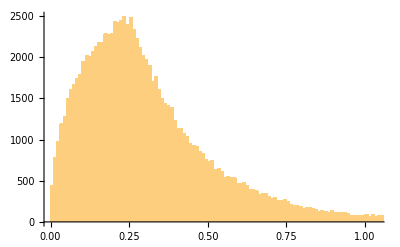

```mathematica
Histogram[Table[scatterE[2.53*^-8],100000],{1*^-9}]
```

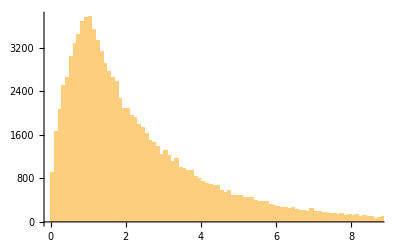

```mathematica
Histogram[Table[scatterE[1.0*^-8],100000],{1*^-9}]
```

```mathematica
hlist1=HistogramList[Table[scatterE[2.53*^-8],1000000],{1.0*^-9}];
```

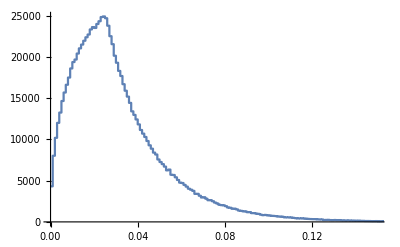

```mathematica
ListStepPlot[Transpose[{10^6 Drop[hlist1[[1]],-1],hlist1[[2]]}],PlotRange->{{0,0.15},All}]
```

```mathematica
plotData[hlist_,f_]:=Transpose[{10^6 Drop[hlist[[1]],-1],f hlist[[2]]/Total[hlist[[2]]]}];
```

```mathematica
factor = 0.082572 0.025 csElasticH[2.53*^-8]/(4π 20.5^2)
```

0.0000117585

```mathematica
data1=plotData[hlist1,factor];
```

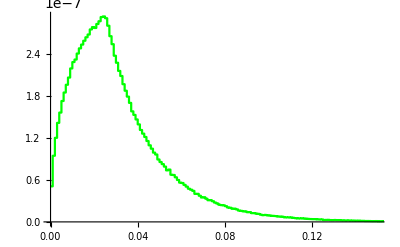

```mathematica
plot1=ListStepPlot[data1,PlotRange->{{0,0.15},All},PlotStyle->Green]
```

```mathematica
newTally[t_,n_,bin_]:=(Clear[t];t["table"]=Table[0,n];t["binsize"]=bin;)
```

```mathematica
scoreTally[t_,x_,score_]:=Module[{ibin,table},ibin=Ceiling[x/t["binsize"]];table=t["table"];
If[ibin>0&&ibin≤Length[t["table"]],table[[ibin]]+=score];
t["table"]=table;]
```

```mathematica
clearTally[t_]:=Module[{n=Length[t["table"]]},t["table"]=Table[0,n];]
```

```mathematica
listToPlotTally[t_,scale_:1]:=Module[{table=t["table"],n,bin=t["binsize"]},n=Length[table];Table[{(i-1) bin,scale table[[i]]},{i,1,n}]];
```

```mathematica
clearTally[talFlux]
```

```mathematica
newTally[talFlux,150,0.001]
```

```mathematica
erg=2.53*^-8;
```

```mathematica
For[i=0,i<10000,i++,Module[{pathLen},erg=scatterE[erg];pathLen=1/(0.082572 csElasticH[erg]);scoreTally[talFlux,10^6 erg,pathLen];]]
```

```mathematica
Module[{erg=2.53*^-8,pathLen,reps=100000},
clearTally[talFlux];
For[i=0,i<reps,i++,erg=scatterE[erg];pathLen=1/(0.082572 csElasticH[erg]);scoreTally[talFlux,10^6 erg,pathLen/reps];]]
```

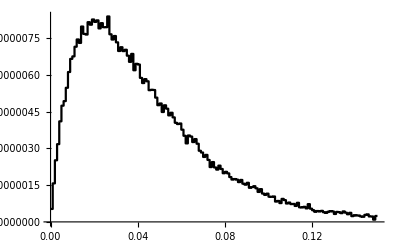

```mathematica
ListStepPlot[listToPlotTally[talFlux,1.2*^-3],PlotStyle->Black]
```

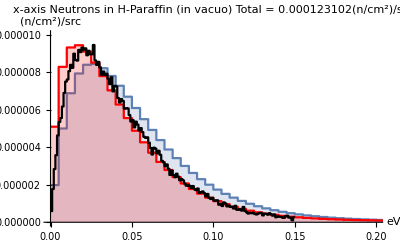

```mathematica
Show[hist18104,histGmThickHwax,ListStepPlot[listToPlotTally[talFlux,1.35*^-3],PlotStyle->Black]]
```

```mathematica
csElasticH=Interpolation[ImportString["1.00000000e-11      1.16053e+03
1.03125000e-11      1.14282e+03
1.06250000e-11      1.12589e+03
1.09375000e-11      1.10969e+03
1.12500000e-11      1.09418e+03
1.15625000e-11      1.07930e+03
1.18750000e-11      1.06500e+03
1.21875000e-11      1.05127e+03
1.25000000e-11      1.03805e+03
1.28125000e-11      1.02531e+03
1.31250000e-11      1.01304e+03
1.34375000e-11      1.00119e+03
1.37500000e-11      9.89753e+02
1.43750000e-11      9.68006e+02
1.50000000e-11      9.47632e+02
1.56250000e-11      9.28494e+02
1.62500000e-11      9.10471e+02
1.68750000e-11      8.93458e+02
1.75000000e-11      8.77366e+02
1.81250000e-11      8.62113e+02
1.87500000e-11      8.47630e+02
1.93750000e-11      8.33853e+02
2.00000000e-11      8.20727e+02
2.09375000e-11      8.02152e+02
2.18750000e-11      7.84785e+02
2.28125000e-11      7.68499e+02
2.37500000e-11      7.53188e+02
2.46875000e-11      7.38758e+02
2.56250000e-11      7.25127e+02
2.65625000e-11      7.12224e+02
2.75000000e-11      6.99988e+02
2.84375000e-11      6.88361e+02
2.93750000e-11      6.77296e+02
3.03125000e-11      6.66748e+02
3.12500000e-11      6.56679e+02
3.21875000e-11      6.47053e+02
3.31250000e-11      6.37839e+02
3.40625000e-11      6.29007e+02
3.50000000e-11      6.20534e+02
3.59375000e-11      6.12394e+02
3.68750000e-11      6.04567e+02
3.78125000e-11      5.97032e+02
3.87500000e-11      5.89773e+02
3.96875000e-11      5.82773e+02
4.06250000e-11      5.76016e+02
4.25000000e-11      5.63181e+02
4.43750000e-11      5.51168e+02
4.62500000e-11      5.39893e+02
4.81250000e-11      5.29285e+02
5.00000000e-11      5.19278e+02
5.15625000e-11      5.11361e+02
5.31250000e-11      5.03795e+02
5.46875000e-11      4.96556e+02
5.62500000e-11      4.89621e+02
5.78125000e-11      4.82969e+02
5.93750000e-11      4.76581e+02
6.09375000e-11      4.70441e+02
6.25000000e-11      4.64533e+02
6.40625000e-11      4.58842e+02
6.56250000e-11      4.53356e+02
6.71875000e-11      4.48063e+02
6.87500000e-11      4.42951e+02
7.18750000e-11      4.33233e+02
7.50000000e-11      4.24128e+02
7.81250000e-11      4.15576e+02
8.12500000e-11      4.07523e+02
8.43750000e-11      3.99921e+02
8.75000000e-11      3.92731e+02
9.06250000e-11      3.85916e+02
9.37500000e-11      3.79445e+02
9.68750000e-11      3.73290e+02
1.00000000e-10      3.67426e+02
1.03125000e-10      3.61831e+02
1.06250000e-10      3.56485e+02
1.09375000e-10      3.51370e+02
1.12500000e-10      3.46470e+02
1.15625000e-10      3.41770e+02
1.18750000e-10      3.37257e+02
1.21875000e-10      3.32918e+02
1.25000000e-10      3.28744e+02
1.28125000e-10      3.24724e+02
1.31250000e-10      3.20848e+02
1.34375000e-10      3.17108e+02
1.37500000e-10      3.13497e+02
1.43750000e-10      3.06631e+02
1.50000000e-10      3.00199e+02
1.56250000e-10      2.94158e+02
1.62500000e-10      2.88470e+02
1.68750000e-10      2.83100e+02
1.75000000e-10      2.78022e+02
1.81250000e-10      2.73209e+02
1.87500000e-10      2.68639e+02
1.93750000e-10      2.64292e+02
2.00000000e-10      2.60151e+02
2.09375000e-10      2.54291e+02
2.18750000e-10      2.48813e+02
2.28125000e-10      2.43677e+02
2.37500000e-10      2.38848e+02
2.46875000e-10      2.34298e+02
2.56250000e-10      2.30000e+02
2.65625000e-10      2.25933e+02
2.75000000e-10      2.22076e+02
2.84375000e-10      2.18411e+02
2.93750000e-10      2.14924e+02
3.03125000e-10      2.11600e+02
3.12500000e-10      2.08428e+02
3.21875000e-10      2.05395e+02
3.31250000e-10      2.02492e+02
3.40625000e-10      1.99711e+02
3.50000000e-10      1.97042e+02
3.59375000e-10      1.94479e+02
3.68750000e-10      1.92014e+02
3.78125000e-10      1.89642e+02
3.87500000e-10      1.87357e+02
3.96875000e-10      1.85154e+02
4.06250000e-10      1.83027e+02
4.25000000e-10      1.78988e+02
4.43750000e-10      1.75209e+02
4.62500000e-10      1.71662e+02
4.81250000e-10      1.68326e+02
5.00000000e-10      1.65180e+02
5.15625000e-10      1.62691e+02
5.31250000e-10      1.60314e+02
5.46875000e-10      1.58039e+02
5.62500000e-10      1.55860e+02
5.78125000e-10      1.53771e+02
5.93750000e-10      1.51765e+02
6.09375000e-10      1.49837e+02
6.25000000e-10      1.47982e+02
6.40625000e-10      1.46196e+02
6.56250000e-10      1.44474e+02
6.71875000e-10      1.42814e+02
6.87500000e-10      1.41210e+02
7.18750000e-10      1.38162e+02
7.50000000e-10      1.35308e+02
7.81250000e-10      1.32628e+02
8.12500000e-10      1.30105e+02
8.43750000e-10      1.27724e+02
8.75000000e-10      1.25474e+02
9.06250000e-10      1.23341e+02
9.37500000e-10      1.21317e+02
9.68750000e-10      1.19392e+02
1.00000000e-09      1.17559e+02
1.03125000e-09      1.15811e+02
1.06250000e-09      1.14141e+02
1.09375000e-09      1.12544e+02
1.12500000e-09      1.11015e+02
1.15625000e-09      1.09548e+02
1.18750000e-09      1.08140e+02
1.21875000e-09      1.06788e+02
1.25000000e-09      1.05487e+02
1.28125000e-09      1.04234e+02
1.31250000e-09      1.03027e+02
1.34375000e-09      1.01863e+02
1.37500000e-09      1.00739e+02
1.43750000e-09      9.86033e+01
1.50000000e-09      9.66042e+01
1.56250000e-09      9.47279e+01
1.62500000e-09      9.29623e+01
1.68750000e-09      9.12971e+01
1.75000000e-09      8.97232e+01
1.81250000e-09      8.82326e+01
1.87500000e-09      8.68183e+01
1.93750000e-09      8.54741e+01
2.00000000e-09      8.41944e+01
2.09375000e-09      8.23853e+01
2.18750000e-09      8.06958e+01
2.28125000e-09      7.91134e+01
2.37500000e-09      7.76275e+01
2.46875000e-09      7.62287e+01
2.56250000e-09      7.49090e+01
2.65625000e-09      7.36613e+01
2.75000000e-09      7.24794e+01
2.84375000e-09      7.13578e+01
2.93750000e-09      7.02915e+01
3.03125000e-09      6.92764e+01
3.12500000e-09      6.83084e+01
3.21875000e-09      6.73841e+01
3.31250000e-09      6.65005e+01
3.40625000e-09      6.56545e+01
3.50000000e-09      6.48438e+01
3.59375000e-09      6.40659e+01
3.68750000e-09      6.33187e+01
3.78125000e-09      6.26004e+01
3.87500000e-09      6.19091e+01
3.96875000e-09      6.12433e+01
4.06250000e-09      6.06014e+01
4.25000000e-09      5.93840e+01
4.43750000e-09      5.82473e+01
4.62500000e-09      5.71830e+01
4.81250000e-09      5.61839e+01
5.00000000e-09      5.52437e+01
5.15625000e-09      5.45013e+01
5.31250000e-09      5.37933e+01
5.46875000e-09      5.31171e+01
5.62500000e-09      5.24706e+01
5.78125000e-09      5.18517e+01
5.93750000e-09      5.12585e+01
6.09375000e-09      5.06894e+01
6.25000000e-09      5.01428e+01
6.40625000e-09      4.96174e+01
6.56250000e-09      4.91118e+01
6.71875000e-09      4.86249e+01
6.87500000e-09      4.81555e+01
7.18750000e-09      4.72658e+01
7.50000000e-09      4.64354e+01
7.81250000e-09      4.56583e+01
8.12500000e-09      4.49292e+01
8.43750000e-09      4.42436e+01
8.75000000e-09      4.35976e+01
9.06250000e-09      4.29875e+01
9.37500000e-09      4.24103e+01
9.68750000e-09      4.18634e+01
1.00000000e-08      4.13442e+01
1.03125000e-08      4.08506e+01
1.06250000e-08      4.03807e+01
1.09375000e-08      3.99328e+01
1.12500000e-08      3.95052e+01
1.15625000e-08      3.90965e+01
1.18750000e-08      3.87055e+01
1.21875000e-08      3.83310e+01
1.25000000e-08      3.79720e+01
1.28125000e-08      3.76274e+01
1.31250000e-08      3.72964e+01
1.34375000e-08      3.69781e+01
1.37500000e-08      3.66718e+01
1.43750000e-08      3.60926e+01
1.50000000e-08      3.55538e+01
1.56250000e-08      3.50512e+01
1.62500000e-08      3.45811e+01
1.68750000e-08      3.41405e+01
1.75000000e-08      3.37265e+01
1.81250000e-08      3.33368e+01
1.87500000e-08      3.29693e+01
1.93750000e-08      3.26220e+01
2.00000000e-08      3.22933e+01
2.06625000e-08      3.19636e+01
2.13250000e-08      3.16516e+01
2.19875000e-08      3.13558e+01
2.26500000e-08      3.10751e+01
2.33125000e-08      3.08082e+01
2.39750000e-08      3.05542e+01
2.46375000e-08      3.03122e+01
2.53000000e-08      3.00812e+01
2.64578200e-08      2.97021e+01
2.76156300e-08      2.93512e+01
2.87734400e-08      2.90253e+01
2.99312500e-08      2.87220e+01
3.10890700e-08      2.84389e+01
3.22468800e-08      2.81741e+01
3.34046900e-08      2.79258e+01
3.45625000e-08      2.76927e+01
3.55273500e-08      2.75089e+01
3.64921900e-08      2.73340e+01
3.74570400e-08      2.71674e+01
3.84218800e-08      2.70084e+01
3.93867300e-08      2.68566e+01
4.03515700e-08      2.67114e+01
4.13164100e-08      2.65725e+01
4.22812500e-08      2.64395e+01
4.42109400e-08      2.61897e+01
4.61406300e-08      2.59594e+01
4.80703200e-08      2.57464e+01
5.00000000e-08      2.55489e+01
5.15625000e-08      2.53991e+01
5.31250000e-08      2.52578e+01
5.46875000e-08      2.51240e+01
5.62500000e-08      2.49974e+01
5.78125000e-08      2.48773e+01
5.93750000e-08      2.47632e+01
6.09375000e-08      2.46547e+01
6.25000000e-08      2.45515e+01
6.40625000e-08      2.44531e+01
6.56250000e-08      2.43592e+01
6.71875000e-08      2.42695e+01
6.87500000e-08      2.41838e+01
7.18750000e-08      2.40232e+01
7.50000000e-08      2.38756e+01
7.81250000e-08      2.37395e+01
8.12500000e-08      2.36137e+01
8.43750000e-08      2.34970e+01
8.75000000e-08      2.33885e+01
9.06250000e-08      2.32873e+01
9.37500000e-08      2.31928e+01
9.68750000e-08      2.31044e+01
1.00000000e-07      2.30213e+01
1.03125000e-07      2.29433e+01
1.06250000e-07      2.28698e+01
1.09375000e-07      2.28005e+01
1.12500000e-07      2.27350e+01
1.15625000e-07      2.26730e+01
1.18750000e-07      2.26142e+01
1.21875000e-07      2.25585e+01
1.25000000e-07      2.25055e+01
1.28125000e-07      2.24551e+01
1.31250000e-07      2.24071e+01
1.34375000e-07      2.23613e+01
1.37500000e-07      2.23175e+01
1.43750000e-07      2.22358e+01
1.50000000e-07      2.21609e+01
1.56250000e-07      2.20919e+01
1.62500000e-07      2.20282e+01
1.68750000e-07      2.19693e+01
1.75000000e-07      2.19145e+01
1.81250000e-07      2.18635e+01
1.87500000e-07      2.18160e+01
1.93750000e-07      2.17715e+01
2.00000000e-07      2.17297e+01
2.09375000e-07      2.16718e+01
2.18750000e-07      2.16188e+01
2.28125000e-07      2.15702e+01
2.37500000e-07      2.15255e+01
2.46875000e-07      2.14841e+01
2.56250000e-07      2.14457e+01
2.65625000e-07      2.14101e+01
2.75000000e-07      2.13769e+01
2.84375000e-07      2.13459e+01
2.93750000e-07      2.13168e+01
3.03125000e-07      2.12896e+01
3.12500000e-07      2.12640e+01
3.21875000e-07      2.12399e+01
3.31250000e-07      2.12171e+01
3.40625000e-07      2.11956e+01
3.50000000e-07      2.11753e+01
3.59375000e-07      2.11560e+01
3.68750000e-07      2.11377e+01
3.78125000e-07      2.11203e+01
3.87500000e-07      2.11037e+01
3.96875000e-07      2.10880e+01
4.06250000e-07      2.10729e+01
4.25000000e-07      2.10448e+01
4.43750000e-07      2.10191e+01
4.62500000e-07      2.09954e+01
5.00000000e-07      2.09535e+01
5.31250000e-07      2.09230e+01
5.62500000e-07      2.08960e+01
5.93750000e-07      2.08718e+01
6.25000000e-07      2.08500e+01
6.87500000e-07      2.08123e+01
7.50000000e-07      2.07810e+01
8.12500000e-07      2.07544e+01
8.75000000e-07      2.07317e+01
9.37500000e-07      2.07119e+01
1.00000000e-06      2.06947e+01
1.06250000e-06      2.06795e+01
1.12500000e-06      2.06659e+01
1.18750000e-06      2.06538e+01
1.25000000e-06      2.06429e+01
1.37500000e-06      2.06241e+01
1.50000000e-06      2.06084e+01
1.62500000e-06      2.05951e+01
1.75000000e-06      2.05837e+01
1.87500000e-06      2.05738e+01
2.00000000e-06      2.05652e+01
2.18750000e-06      2.05541e+01
2.37500000e-06      2.05447e+01
2.56250000e-06      2.05367e+01
2.75000000e-06      2.05298e+01
2.93750000e-06      2.05238e+01
3.12500000e-06      2.05185e+01
3.31250000e-06      2.05137e+01
3.50000000e-06      2.05095e+01
3.87500000e-06      2.05023e+01
4.25000000e-06      2.04964e+01
4.62500000e-06      2.04914e+01
5.00000000e-06      2.04872e+01
5.31250000e-06      2.04841e+01
5.62500000e-06      2.04813e+01
5.93750000e-06      2.04789e+01
6.25000000e-06      2.04766e+01
6.87500000e-06      2.04728e+01
7.50000000e-06      2.04696e+01
8.12500000e-06      2.04668e+01
8.75000000e-06      2.04645e+01
9.37500000e-06      2.04624e+01
1.00000000e-05      2.04606e+01
1.06250000e-05      2.04590e+01
1.12500000e-05      2.04576e+01
1.18750000e-05      2.04563e+01
1.25000000e-05      2.04551e+01
1.37500000e-05      2.04530e+01
1.50000000e-05      2.04513e+01
1.62500000e-05      2.04498e+01
1.75000000e-05      2.04485e+01
1.87500000e-05      2.04474e+01
2.00000000e-05      2.04463e+01
2.18750000e-05      2.04450e+01
2.37500000e-05      2.04438e+01
2.56250000e-05      2.04427e+01
2.75000000e-05      2.04418e+01
2.93750000e-05      2.04409e+01
3.12500000e-05      2.04402e+01
3.31250000e-05      2.04394e+01
3.50000000e-05      2.04388e+01
3.87500000e-05      2.04375e+01
4.25000000e-05      2.04364e+01
4.62500000e-05      2.04354e+01
5.00000000e-05      2.04345e+01
5.31250000e-05      2.04338e+01
5.62500000e-05      2.04331e+01
5.93750000e-05      2.04324e+01
6.25000000e-05      2.04318e+01
6.87500000e-05      2.04306e+01
7.50000000e-05      2.04294e+01
8.12500000e-05      2.04283e+01
8.75000000e-05      2.04273e+01
9.37500000e-05      2.04262e+01
1.00000000e-04      2.04252e+01
1.06250000e-04      2.04242e+01
1.12500000e-04      2.04232e+01
1.18750000e-04      2.04223e+01
1.25000000e-04      2.04213e+01
1.37500000e-04      2.04195e+01
1.50000000e-04      2.04176e+01
1.62500000e-04      2.04158e+01
1.75000000e-04      2.04140e+01
1.87500000e-04      2.04122e+01
2.00000000e-04      2.04105e+01
2.18750000e-04      2.04079e+01
2.37500000e-04      2.04053e+01
2.56250000e-04      2.04027e+01
2.75000000e-04      2.04001e+01
2.93750000e-04      2.03975e+01
3.12500000e-04      2.03950e+01
3.31250000e-04      2.03924e+01
3.50000000e-04      2.03898e+01
3.87500000e-04      2.03848e+01
4.25000000e-04      2.03797e+01
4.62500000e-04      2.03746e+01
5.00000000e-04      2.03695e+01
5.31250000e-04      2.03654e+01
5.62500000e-04      2.03612e+01
5.93750000e-04      2.03570e+01
6.25000000e-04      2.03528e+01
6.87500000e-04      2.03444e+01
7.50000000e-04      2.03361e+01
8.12500000e-04      2.03278e+01
8.75000000e-04      2.03194e+01
9.37500000e-04      2.03111e+01
1.00000000e-03      2.03027e+01
1.06250000e-03      2.02945e+01
1.12500000e-03      2.02863e+01
1.18750000e-03      2.02780e+01
1.25000000e-03      2.02698e+01
1.37500000e-03      2.02533e+01
1.50000000e-03      2.02368e+01
1.62500000e-03      2.02204e+01
1.75000000e-03      2.02039e+01
1.87500000e-03      2.01875e+01
2.00000000e-03      2.01710e+01
2.12500000e-03      2.01548e+01
2.25000000e-03      2.01386e+01
2.37500000e-03      2.01223e+01
2.50000000e-03      2.01061e+01
2.75000000e-03      2.00737e+01
3.00000000e-03      2.00413e+01
3.25000000e-03      2.00093e+01
3.50000000e-03      1.99774e+01
3.75000000e-03      1.99454e+01
4.00000000e-03      1.99135e+01
4.25000000e-03      1.98820e+01
4.50000000e-03      1.98505e+01
4.75000000e-03      1.98190e+01
5.00000000e-03      1.97876e+01
5.25000000e-03      1.97565e+01
5.50000000e-03      1.97255e+01
5.75000000e-03      1.96945e+01
6.00000000e-03      1.96634e+01
6.25000000e-03      1.96328e+01
6.50000000e-03      1.96023e+01
6.75000000e-03      1.95717e+01
7.00000000e-03      1.95411e+01
7.50000000e-03      1.94808e+01
8.00000000e-03      1.94205e+01
8.50000000e-03      1.93610e+01
9.00000000e-03      1.93016e+01
9.50000000e-03      1.92429e+01
1.00000000e-02      1.91843e+01
1.05000000e-02      1.91269e+01
1.10000000e-02      1.90695e+01
1.15000000e-02      1.90121e+01
1.20000000e-02      1.89547e+01
1.25000000e-02      1.88988e+01
1.30000000e-02      1.88430e+01
1.35000000e-02      1.87871e+01
1.40000000e-02      1.87313e+01
1.50000000e-02      1.86226e+01
1.60000000e-02      1.85139e+01
1.70000000e-02      1.84080e+01
1.80000000e-02      1.83022e+01
1.90000000e-02      1.81992e+01
2.00000000e-02      1.80961e+01
2.10000000e-02      1.79957e+01
2.20000000e-02      1.78953e+01
2.30000000e-02      1.77974e+01
2.40000000e-02      1.76996e+01
2.50000000e-02      1.76041e+01
2.60000000e-02      1.75088e+01
2.70000000e-02      1.74157e+01
2.80000000e-02      1.73227e+01
3.00000000e-02      1.71412e+01
3.25000000e-02      1.69237e+01
3.50000000e-02      1.67063e+01
3.75000000e-02      1.65013e+01
4.00000000e-02      1.62964e+01
4.25000000e-02      1.61029e+01
4.50000000e-02      1.59095e+01
4.75000000e-02      1.57265e+01
5.00000000e-02      1.55436e+01
5.25000000e-02      1.53703e+01
5.50000000e-02      1.51971e+01
5.75000000e-02      1.50327e+01
6.00000000e-02      1.48684e+01
6.25000000e-02      1.47123e+01
6.50000000e-02      1.45563e+01
6.75000000e-02      1.44078e+01
7.00000000e-02      1.42594e+01
7.50000000e-02      1.39767e+01
8.00000000e-02      1.37071e+01
8.50000000e-02      1.34499e+01
9.00000000e-02      1.32040e+01
9.50000000e-02      1.29689e+01
1.00000000e-01      1.27438e+01
1.05000000e-01      1.25323e+01
1.10000000e-01      1.23210e+01
1.15000000e-01      1.21260e+01
1.20000000e-01      1.19312e+01
1.25000000e-01      1.17509e+01
1.30000000e-01      1.15707e+01
1.35000000e-01      1.14034e+01
1.40000000e-01      1.12363e+01
1.50000000e-01      1.09251e+01
1.60000000e-01      1.06348e+01
1.70000000e-01      1.03634e+01
1.80000000e-01      1.01089e+01
1.90000000e-01      9.86993e+00
2.00000000e-01      9.64500e+00
2.10000000e-01      9.43866e+00
2.20000000e-01      9.23249e+00
2.30000000e-01      9.04771e+00
2.40000000e-01      8.86309e+00
2.50000000e-01      8.69659e+00
2.60000000e-01      8.53025e+00
2.70000000e-01      8.37938e+00
2.80000000e-01      8.22865e+00
3.00000000e-01      7.95398e+00
3.20000000e-01      7.70268e+00
3.40000000e-01      7.47178e+00
3.60000000e-01      7.25882e+00
3.80000000e-01      7.06169e+00
4.00000000e-01      6.87863e+00
4.20000000e-01      6.70812e+00
4.40000000e-01      6.54885e+00
4.60000000e-01      6.39968e+00
4.80000000e-01      6.25964e+00
5.00000000e-01      6.12788e+00
5.25000000e-01      5.97884e+00
5.50000000e-01      5.82990e+00
5.75000000e-01      5.69966e+00
6.00000000e-01      5.56952e+00
6.25000000e-01      5.45455e+00
6.50000000e-01      5.33965e+00
6.75000000e-01      5.23721e+00
7.00000000e-01      5.13485e+00
7.50000000e-01      4.95093e+00
8.00000000e-01      4.78460e+00
8.50000000e-01      4.63323e+00
9.00000000e-01      4.49469e+00
9.50000000e-01      4.36726e+00
1.00000000e+00      4.24951e+00
1.10000000e+00      4.03846e+00
1.20000000e+00      3.85418e+00
1.30000000e+00      3.69127e+00
1.40000000e+00      3.54578e+00
1.50000000e+00      3.41466e+00
1.60000000e+00      3.29561e+00
1.70000000e+00      3.18678e+00
1.80000000e+00      3.08672e+00
1.90000000e+00      2.99424e+00
2.00000000e+00      2.90838e+00
2.20000000e+00      2.75345e+00
2.40000000e+00      2.61697e+00
2.60000000e+00      2.49537e+00
2.80000000e+00      2.38600e+00
3.00000000e+00      2.28686e+00
3.20000000e+00      2.19638e+00
3.40000000e+00      2.11334e+00
3.60000000e+00      2.03675e+00
3.80000000e+00      1.96579e+00
4.00000000e+00      1.89979e+00
4.20000000e+00      1.83821e+00
4.40000000e+00      1.78057e+00
4.60000000e+00      1.72646e+00
4.80000000e+00      1.67556e+00
5.00000000e+00      1.62755e+00
5.20000000e+00      1.58218e+00
5.40000000e+00      1.53923e+00
5.60000000e+00      1.49849e+00
5.80000000e+00      1.45979e+00
6.00000000e+00      1.42297e+00
6.20000000e+00      1.38790e+00
6.40000000e+00      1.35443e+00
6.60000000e+00      1.32247e+00
6.80000000e+00      1.29191e+00
7.00000000e+00      1.26265e+00
7.50000000e+00      1.19469e+00
8.00000000e+00      1.13326e+00
8.50000000e+00      1.07744e+00
9.00000000e+00      1.02650e+00
9.50000000e+00      9.79812e-01
1.00000000e+01      9.36875e-01
1.05000000e+01      8.97253e-01
1.10000000e+01      8.60580e-01
1.15000000e+01      8.26542e-01
1.20000000e+01      7.94868e-01
1.25000000e+01      7.65326e-01
1.30000000e+01      7.37709e-01
1.35000000e+01      7.11841e-01
1.40000000e+01      6.87562e-01
1.45000000e+01      6.64735e-01
1.50000000e+01      6.43236e-01
1.55000000e+01      6.22955e-01
1.60000000e+01      6.03793e-01
1.65000000e+01      5.85662e-01
1.70000000e+01      5.68484e-01
1.75000000e+01      5.52186e-01
1.80000000e+01      5.36705e-01
1.85000000e+01      5.21980e-01
1.90000000e+01      5.07960e-01
1.95000000e+01      4.94595e-01
2.00000000e+01      4.81841e-01","Table"]];
```

```mathematica
csElasticH[2.53*^-8]
```

30.0812

```mathematica
hlist1
```

{{0.,1.×10^-9,2.×10^-9,3.×10^-9,4.×10^-9,5.×10^-9,6.×10^-9,7.×10^-9,8.×10^-9,9.×10^-9,1.×10^-8,1.1×10^-8,1.2×10^-8,1.3×10^-8,1.4×10^-8,1.5×10^-8,1.6×10^-8,1.7×10^-8,1.8×10^-8,1.9×10^-8,2.×10^-8,2.1×10^-8,2.2×10^-8,2.3×10^-8,2.4×10^-8,2.5×10^-8,2.6×10^-8,2.7×10^-8,2.8×10^-8,2.9×10^-8,3.×10^-8,3.1×10^-8,3.2×10^-8,3.3×10^-8,3.4×10^-8,3.5×10^-8,3.6×10^-8,3.7×10^-8,3.8×10^-8,3.9×10^-8,4.×10^-8,4.1×10^-8,4.2×10^-8,4.3×10^-8,4.4×10^-8,4.5×10^-8,4.6×10^-8,4.7×10^-8,4.8×10^-8,4.9×10^-8,5.×10^-8,5.1×10^-8,5.2×10^-8,5.3×10^-8,5.4×10^-8,5.5×10^-8,5.6×10^-8,5.7×10^-8,5.8×10^-8,5.9×10^-8,6.×10^-8,6.1×10^-8,6.2×10^-8,6.3×10^-8,6.4×10^-8,6.5×10^-8,6.6×10^-8,6.7×10^-8,6.8×10^-8,6.9×10^-8,7.×10^-8,7.1×10^-8,7.2×10^-8,7.3×10^-8,7.4×10^-8,7.5×10^-8,7.6×10^-8,7.7×10^-8,7.8×10^-8,7.9×10^-8,8.×10^-8,8.1×10^-8,8.2×10^-8,8.3×10^-8,8.4×10^-8,8.5×10^-8,8.6×10^-8,8.7×10^-8,8.8×10^-8,8.9×10^-8,9.×10^-8,9.1×10^-8,9.2×10^-8,9.3×10^-8,9.4×10^-8,9.5×10^-8,9.6×10^-8,9.7×10^-8,9.8×10^-8,9.9×10^-8,1.×10^-7,1.01×10^-7,1.02×10^-7,1.03×10^-7,1.04×10^-7,1.05×10^-7,1.06×10^-7,1.07×10^-7,1.08×10^-7,1.09×10^-7,1.1×10^-7,1.11×10^-7,1.12×10^-7,1.13×10^-7,1.14×10^-7,1.15×10^-7,1.16×10^-7,1.17×10^-7,1.18×10^-7,1.19×10^-7,1.2×10^-7,1.21×10^-7,1.22×10^-7,1.23×10^-7,1.24×10^-7,1.25×10^-7,1.26×10^-7,1.27×10^-7,1.28×10^-7,1.29×10^-7,1.3×10^-7,1.31×10^-7,1.32×10^-7,1.33×10^-7,1.34×10^-7,1.35×10^-7,1.36×10^-7,1.37×10^-7,1.38×10^-7,1.39×10^-7,1.4×10^-7,1.41×10^-7,1.42×10^-7,1.43×10^-7,1.44×10^-7,1.45×10^-7,1.46×10^-7,1.47×10^-7,1.48×10^-7,1.49×10^-7,1.5×10^-7,1.51×10^-7,1.52×10^-7,1.53×10^-7,1.54×10^-7,1.55×10^-7,1.56×10^-7,1.57×10^-7,1.58×10^-7,1.59×10^-7,1.6×10^-7,1.61×10^-7,1.62×10^-7,1.63×10^-7,1.64×10^-7,1.65×10^-7,1.66×10^-7,1.67×10^-7,1.68×10^-7,1.69×10^-7,1.7×10^-7,1.71×10^-7,1.72×10^-7,1.73×10^-7,1.74×10^-7,1.75×10^-7,1.76×10^-7,1.77×10^-7,1.78×10^-7,1.79×10^-7,1.8×10^-7,1.81×10^-7,1.82×10^-7,1.83×10^-7,1.84×10^-7,1.85×10^-7,1.86×10^-7,1.87×10^-7,1.88×10^-7,1.89×10^-7,1.9×10^-7,1.91×10^-7,1.92×10^-7,1.93×10^-7,1.94×10^-7,1.95×10^-7,1.96×10^-7,1.97×10^-7,1.98×10^-7,1.99×10^-7,2.×10^-7,2.01×10^-7,2.02×10^-7,2.03×10^-7,2.04×10^-7,2.05×10^-7,2.06×10^-7,2.07×10^-7,2.08×10^-7,2.09×10^-7,2.1×10^-7,2.11×10^-7,2.12×10^-7,2.13×10^-7,2.14×10^-7,2.15×10^-7,2.16×10^-7,2.17×10^-7,2.18×10^-7,2.19×10^-7,2.2×10^-7,2.21×10^-7,2.22×10^-7,2.23×10^-7,2.24×10^-7,2.25×10^-7,2.26×10^-7,2.27×10^-7,2.28×10^-7,2.29×10^-7,2.3×10^-7,2.31×10^-7,2.32×10^-7,2.33×10^-7,2.34×10^-7,2.35×10^-7,2.36×10^-7,2.37×10^-7,2.38×10^-7,2.39×10^-7,2.4×10^-7,2.41×10^-7,2.42×10^-7,2.43×10^-7,2.44×10^-7,2.45×10^-7,2.46×10^-7,2.47×10^-7,2.48×10^-7,2.49×10^-7,2.5×10^-7,2.51×10^-7,2.52×10^-7,2.53×10^-7,2.54×10^-7,2.55×10^-7,2.56×10^-7,2.57×10^-7,2.58×10^-7,2.59×10^-7,2.6×10^-7,2.61×10^-7,2.62×10^-7,2.63×10^-7,2.64×10^-7,2.65×10^-7,2.66×10^-7,2.67×10^-7,2.68×10^-7,2.69×10^-7,2.7×10^-7,2.71×10^-7,2.72×10^-7,2.73×10^-7,2.74×10^-7,2.75×10^-7,2.76×10^-7,2.77×10^-7,2.78×10^-7,2.79×10^-7,2.8×10^-7,2.81×10^-7,2.82×10^-7,2.83×10^-7,2.84×10^-7,2.85×10^-7,2.86×10^-7,2.87×10^-7,2.88×10^-7,2.89×10^-7,2.9×10^-7,2.91×10^-7,2.92×10^-7,2.93×10^-7,2.94×10^-7,2.95×10^-7,2.96×10^-7,2.97×10^-7,2.98×10^-7,2.99×10^-7,3.×10^-7,3.01×10^-7,3.02×10^-7,3.03×10^-7,3.04×10^-7,3.05×10^-7,3.06×10^-7,3.07×10^-7,3.08×10^-7,3.09×10^-7,3.1×10^-7,3.11×10^-7,3.12×10^-7,3.13×10^-7,3.14×10^-7,3.15×10^-7,3.16×10^-7,3.17×10^-7,3.18×10^-7,3.19×10^-7,3.2×10^-7,3.21×10^-7,3.22×10^-7,3.23×10^-7,3.24×10^-7,3.25×10^-7,3.26×10^-7,3.27×10^-7,3.28×10^-7,3.29×10^-7,3.3×10^-7,3.31×10^-7,3.32×10^-7,3.33×10^-7,3.34×10^-7,3.35×10^-7,3.36×10^-7,3.37×10^-7,3.38×10^-7,3.39×10^-7,3.4×10^-7,3.41×10^-7,3.42×10^-7,3.43×10^-7,3.44×10^-7,3.45×10^-7,3.46×10^-7,3.47×10^-7,3.48×10^-7,3.49×10^-7,3.5×10^-7,3.51×10^-7,3.52×10^-7,3.53×10^-7,3.54×10^-7,3.55×10^-7,3.56×10^-7,3.57×10^-7},{4312,8020,10194,12009,13257,14659,15689,16629,17505,18608,19381,19688,20415,21043,21502,21965,22387,22723,23339,23621,23518,23999,24333,24843,24912,24698,23789,22520,21551,20150,19299,18311,17692,16699,15906,15191,14433,13406,12975,12425,11824,11146,10702,10298,9809,9288,8877,8400,8172,7571,7261,7006,6705,6249,6345,5717,5687,5408,5083,4761,4718,4487,4277,4025,3901,3762,3399,3403,3171,2958,2992,2811,2628,2640,2507,2340,2231,2079,2030,2011,1904,1745,1714,1588,1607,1519,1373,1339,1279,1272,1175,1185,1063,1066,999,969,879,816,846,797,779,738,723,700,646,652,624,550,552,554,532,489,450,420,424,439,403,385,358,345,334,333,302,303,294,232,238,248,220,209,229,209,217,184,171,176,171,172,156,151,135,151,123,126,108,108,104,93,90,98,72,83,81,86,77,73,75,60,71,55,56,52,45,46,45,50,42,50,51,39,43,38,32,25,39,37,17,22,23,30,34,36,23,19,19,15,20,23,21,11,11,16,13,9,18,4,11,17,9,14,14,10,14,13,12,9,10,9,6,9,3,5,8,9,7,5,4,12,2,5,9,5,2,2,5,2,6,5,7,2,4,2,3,3,3,1,2,2,2,3,2,3,0,2,3,1,4,2,0,2,1,1,0,1,0,1,2,1,1,3,1,1,0,1,2,0,1,0,0,0,0,0,0,2,1,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
tally18104
```

{{0.,5.×10^-9,1.×10^-8,1.5×10^-8,2.×10^-8,2.5×10^-8,3.×10^-8,3.5×10^-8,4.×10^-8,4.5×10^-8,5.×10^-8,5.5×10^-8,6.×10^-8,6.5×10^-8,7.×10^-8,7.5×10^-8,8.×10^-8,8.5×10^-8,9.×10^-8,9.5×10^-8,1.×10^-7,1.05×10^-7,1.1×10^-7,1.15×10^-7,1.2×10^-7,1.25×10^-7,1.3×10^-7,1.35×10^-7,1.4×10^-7,1.45×10^-7,1.5×10^-7,1.55×10^-7,1.6×10^-7,1.65×10^-7,1.7×10^-7,1.75×10^-7,1.8×10^-7,1.85×10^-7,1.9×10^-7,1.95×10^-7,2.×10^-7,2.05×10^-7,2.1×10^-7,2.15×10^-7,2.2×10^-7,2.25×10^-7,2.3×10^-7,2.35×10^-7,2.4×10^-7,2.45×10^-7,2.5×10^-7,2.55×10^-7,2.6×10^-7,2.65×10^-7,2.7×10^-7,2.75×10^-7,2.8×10^-7,2.85×10^-7,2.9×10^-7,2.95×10^-7,3.×10^-7,3.05×10^-7,3.1×10^-7,3.15×10^-7,3.2×10^-7,3.25×10^-7,3.3×10^-7,3.35×10^-7,3.4×10^-7,3.45×10^-7,3.5×10^-7,3.55×10^-7,3.6×10^-7,3.65×10^-7,3.7×10^-7,3.75×10^-7,3.8×10^-7,3.85×10^-7,3.9×10^-7,3.95×10^-7,4.×10^-7,4.05×10^-7,4.1×10^-7,4.15×10^-7,4.2×10^-7,4.25×10^-7,4.3×10^-7,4.35×10^-7,4.4×10^-7,4.45×10^-7,4.5×10^-7,4.55×10^-7,4.6×10^-7,4.65×10^-7,4.7×10^-7,4.75×10^-7,4.8×10^-7,4.85×10^-7,4.9×10^-7,4.95×10^-7,5.×10^-7,5.05×10^-7,5.1×10^-7,5.15×10^-7,5.2×10^-7,5.25×10^-7,5.3×10^-7,5.35×10^-7,5.4×10^-7,5.45×10^-7,5.5×10^-7,5.55×10^-7,5.6×10^-7,5.65×10^-7,5.7×10^-7,5.75×10^-7,5.8×10^-7,5.85×10^-7,5.9×10^-7,5.95×10^-7,6.×10^-7,6.05×10^-7,6.1×10^-7,6.15×10^-7,6.2×10^-7,6.25×10^-7,6.3×10^-7,6.35×10^-7,6.4×10^-7,6.45×10^-7,6.5×10^-7,6.55×10^-7,6.6×10^-7,6.65×10^-7,6.7×10^-7,6.75×10^-7,6.8×10^-7,6.85×10^-7,6.9×10^-7,6.95×10^-7,7.×10^-7,7.05×10^-7,7.1×10^-7,7.15×10^-7,7.2×10^-7,7.25×10^-7,7.3×10^-7,7.35×10^-7,7.4×10^-7,7.45×10^-7,7.5×10^-7,7.55×10^-7,7.6×10^-7,7.65×10^-7,7.7×10^-7,7.75×10^-7,7.8×10^-7,7.85×10^-7,7.9×10^-7,7.95×10^-7,8.×10^-7,8.05×10^-7,8.1×10^-7,8.15×10^-7,8.2×10^-7,8.25×10^-7,8.3×10^-7,8.35×10^-7,8.4×10^-7,8.45×10^-7,8.5×10^-7,8.55×10^-7,8.6×10^-7,8.65×10^-7,8.7×10^-7,8.75×10^-7,8.8×10^-7,8.85×10^-7,8.9×10^-7,8.95×10^-7,9.×10^-7,9.05×10^-7,9.1×10^-7,9.15×10^-7,9.2×10^-7,9.25×10^-7,9.3×10^-7,9.35×10^-7,9.4×10^-7,9.45×10^-7,9.5×10^-7,9.55×10^-7,9.6×10^-7,9.65×10^-7,9.7×10^-7,9.75×10^-7,9.8×10^-7,9.85×10^-7,9.9×10^-7,9.95×10^-7,1.×10^-6},{0.,1.98056×10^-6,4.99472×10^-6,6.87313×10^-6,7.92501×10^-6,8.39072×10^-6,8.43887×10^-6,8.206×10^-6,7.79279×10^-6,7.27132×10^-6,6.68855×10^-6,6.0874×10^-6,5.49172×10^-6,4.91829×10^-6,4.3773×10^-6,3.87566×10^-6,3.41689×10^-6,3.00065×10^-6,2.6265×10^-6,2.2952×10^-6,2.00021×10^-6,1.73858×10^-6,1.51179×10^-6,1.31169×10^-6,1.1366×10^-6,9.84294×10^-7,8.53697×10^-7,7.39844×10^-7,6.41556×10^-7,5.56642×10^-7,4.83646×10^-7,4.20019×10^-7,3.65898×10^-7,3.20092×10^-7,2.80485×10^-7,2.46243×10^-7,2.17374×10^-7,1.92096×10^-7,1.71094×10^-7,1.52618×10^-7,1.37206×10^-7,1.23346×10^-7,1.11672×10^-7,1.01918×10^-7,9.33006×10^-8,8.5592×10^-8,7.92234×10^-8,7.37705×10^-8,6.87906×10^-8,6.43569×10^-8,6.07313×10^-8,5.76281×10^-8,5.48331×10^-8,5.23389×10^-8,5.00764×10^-8,4.81759×10^-8,4.67128×10^-8,4.48894×10^-8,4.32493×10^-8,4.21186×10^-8,4.10032×10^-8,3.98843×10^-8,3.84425×10^-8,3.78503×10^-8,3.68173×10^-8,3.6147×10^-8,3.54285×10^-8,3.46011×10^-8,3.4065×10^-8,3.35018×10^-8,3.268×10^-8,3.2224×10^-8,3.15253×10^-8,3.11381×10^-8,3.06082×10^-8,3.0327×10^-8,2.9669×10^-8,2.93947×10^-8,2.91613×10^-8,2.84219×10^-8,2.78767×10^-8,2.76441×10^-8,2.71112×10^-8,2.6833×10^-8,2.64021×10^-8,2.62778×10^-8,2.59469×10^-8,2.56906×10^-8,2.51635×10^-8,2.48504×10^-8,2.46387×10^-8,2.4293×10^-8,2.41224×10^-8,2.37963×10^-8,2.33677×10^-8,2.33755×10^-8,2.29662×10^-8,2.27929×10^-8,2.24465×10^-8,2.22356×10^-8,2.21487×10^-8,2.17096×10^-8,2.14496×10^-8,2.13762×10^-8,2.1047×10^-8,2.09999×10^-8,2.0773×10^-8,2.05024×10^-8,2.02146×10^-8,2.00274×10^-8,1.99915×10^-8,1.97445×10^-8,1.98168×10^-8,1.92755×10^-8,1.94615×10^-8,1.90589×10^-8,1.88298×10^-8,1.85559×10^-8,1.85504×10^-8,1.83203×10^-8,1.8079×10^-8,1.79132×10^-8,1.78048×10^-8,1.75854×10^-8,1.7513×10^-8,1.72444×10^-8,1.72696×10^-8,1.70584×10^-8,1.6759×10^-8,1.67957×10^-8,1.6639×10^-8,1.65283×10^-8,1.63053×10^-8,1.61563×10^-8,1.60588×10^-8,1.58953×10^-8,1.57446×10^-8,1.58754×10^-8,1.56622×10^-8,1.55656×10^-8,1.54399×10^-8,1.53473×10^-8,1.52253×10^-8,1.5086×10^-8,1.4867×10^-8,1.48677×10^-8,1.46911×10^-8,1.46005×10^-8,1.46685×10^-8,1.4449×10^-8,1.42416×10^-8,1.4326×10^-8,1.41869×10^-8,1.39608×10^-8,1.3996×10^-8,1.36206×10^-8,1.39195×10^-8,1.36796×10^-8,1.36592×10^-8,1.3484×10^-8,1.32677×10^-8,1.33079×10^-8,1.31047×10^-8,1.30526×10^-8,1.30922×10^-8,1.29804×10^-8,1.28427×10^-8,1.2919×10^-8,1.28272×10^-8,1.25047×10^-8,1.27773×10^-8,1.25544×10^-8,1.23973×10^-8,1.24555×10^-8,1.23132×10^-8,1.22464×10^-8,1.22653×10^-8,1.22198×10^-8,1.21199×10^-8,1.20538×10^-8,1.20384×10^-8,1.1854×10^-8,1.17429×10^-8,1.17315×10^-8,1.157×10^-8,1.15997×10^-8,1.14289×10^-8,1.1481×10^-8,1.15145×10^-8,1.1353×10^-8,1.13085×10^-8,1.12617×10^-8,1.11221×10^-8,1.11159×10^-8,1.09765×10^-8,1.09478×10^-8,1.10094×10^-8,1.09014×10^-8,1.08581×10^-8,1.08184×10^-8,1.06515×10^-8},{0.,0.0003,0.0003,0.0002,0.0002,0.0002,0.0002,0.0002,0.0003,0.0003,0.0003,0.0003,0.0003,0.0003,0.0003,0.0003,0.0003,0.0003,0.0004,0.0004,0.0004,0.0004,0.0005,0.0005,0.0005,0.0006,0.0006,0.0006,0.0007,0.0007,0.0008,0.0009,0.0009,0.001,0.0011,0.0011,0.0012,0.0013,0.0014,0.0015,0.0016,0.0017,0.0018,0.0019,0.002,0.0021,0.0022,0.0023,0.0024,0.0025,0.0026,0.0027,0.0028,0.0028,0.0029,0.003,0.003,0.0031,0.0032,0.0032,0.0033,0.0033,0.0034,0.0034,0.0035,0.0035,0.0036,0.0036,0.0036,0.0037,0.0037,0.0037,0.0038,0.0038,0.0038,0.0039,0.0039,0.0039,0.0039,0.004,0.004,0.0041,0.0041,0.0041,0.0041,0.0042,0.0042,0.0042,0.0043,0.0043,0.0043,0.0043,0.0043,0.0044,0.0044,0.0044,0.0045,0.0045,0.0045,0.0045,0.0045,0.0046,0.0046,0.0046,0.0047,0.0047,0.0047,0.0047,0.0047,0.0048,0.0048,0.0048,0.0048,0.0049,0.0049,0.0049,0.0049,0.005,0.005,0.005,0.005,0.0051,0.0051,0.0051,0.0051,0.0051,0.0052,0.0052,0.0052,0.0052,0.0053,0.0053,0.0053,0.0053,0.0053,0.0054,0.0054,0.0054,0.0054,0.0054,0.0055,0.0055,0.0055,0.0055,0.0056,0.0056,0.0056,0.0056,0.0056,0.0057,0.0057,0.0057,0.0057,0.0057,0.0057,0.0058,0.0058,0.0058,0.0058,0.0059,0.0058,0.0059,0.0059,0.0059,0.0059,0.006,0.006,0.006,0.006,0.0061,0.0061,0.0061,0.0061,0.0061,0.0061,0.0062,0.0062,0.0062,0.0062,0.0062,0.0062,0.0062,0.0063,0.0063,0.0063,0.0063,0.0064,0.0064,0.0063,0.0064,0.0064,0.0064,0.0064,0.0064,0.0065,0.0065,0.0065,0.0065,0.0065,0.0066,0.0066},{{0.,1.98056×10^-6},{0.005,4.99472×10^-6},{0.01,6.87313×10^-6},{0.015,7.92501×10^-6},{0.02,8.39072×10^-6},{0.025,8.43887×10^-6},{0.03,8.206×10^-6},{0.035,7.79279×10^-6},{0.04,7.27132×10^-6},{0.045,6.68855×10^-6},{0.05,6.0874×10^-6},{0.055,5.49172×10^-6},{0.06,4.91829×10^-6},{0.065,4.3773×10^-6},{0.07,3.87566×10^-6},{0.075,3.41689×10^-6},{0.08,3.00065×10^-6},{0.085,2.6265×10^-6},{0.09,2.2952×10^-6},{0.095,2.00021×10^-6},{0.1,1.73858×10^-6},{0.105,1.51179×10^-6},{0.11,1.31169×10^-6},{0.115,1.1366×10^-6},{0.12,9.84294×10^-7},{0.125,8.53697×10^-7},{0.13,7.39844×10^-7},{0.135,6.41556×10^-7},{0.14,5.56642×10^-7},{0.145,4.83646×10^-7},{0.15,4.20019×10^-7},{0.155,3.65898×10^-7},{0.16,3.20092×10^-7},{0.165,2.80485×10^-7},{0.17,2.46243×10^-7},{0.175,2.17374×10^-7},{0.18,1.92096×10^-7},{0.185,1.71094×10^-7},{0.19,1.52618×10^-7},{0.195,1.37206×10^-7},{0.2,1.23346×10^-7},{0.205,1.11672×10^-7},{0.21,1.01918×10^-7},{0.215,9.33006×10^-8},{0.22,8.5592×10^-8},{0.225,7.92234×10^-8},{0.23,7.37705×10^-8},{0.235,6.87906×10^-8},{0.24,6.43569×10^-8},{0.245,6.07313×10^-8},{0.25,5.76281×10^-8},{0.255,5.48331×10^-8},{0.26,5.23389×10^-8},{0.265,5.00764×10^-8},{0.27,4.81759×10^-8},{0.275,4.67128×10^-8},{0.28,4.48894×10^-8},{0.285,4.32493×10^-8},{0.29,4.21186×10^-8},{0.295,4.10032×10^-8},{0.3,3.98843×10^-8},{0.305,3.84425×10^-8},{0.31,3.78503×10^-8},{0.315,3.68173×10^-8},{0.32,3.6147×10^-8},{0.325,3.54285×10^-8},{0.33,3.46011×10^-8},{0.335,3.4065×10^-8},{0.34,3.35018×10^-8},{0.345,3.268×10^-8},{0.35,3.2224×10^-8},{0.355,3.15253×10^-8},{0.36,3.11381×10^-8},{0.365,3.06082×10^-8},{0.37,3.0327×10^-8},{0.375,2.9669×10^-8},{0.38,2.93947×10^-8},{0.385,2.91613×10^-8},{0.39,2.84219×10^-8},{0.395,2.78767×10^-8},{0.4,2.76441×10^-8},{0.405,2.71112×10^-8},{0.41,2.6833×10^-8},{0.415,2.64021×10^-8},{0.42,2.62778×10^-8},{0.425,2.59469×10^-8},{0.43,2.56906×10^-8},{0.435,2.51635×10^-8},{0.44,2.48504×10^-8},{0.445,2.46387×10^-8},{0.45,2.4293×10^-8},{0.455,2.41224×10^-8},{0.46,2.37963×10^-8},{0.465,2.33677×10^-8},{0.47,2.33755×10^-8},{0.475,2.29662×10^-8},{0.48,2.27929×10^-8},{0.485,2.24465×10^-8},{0.49,2.22356×10^-8},{0.495,2.21487×10^-8},{0.5,2.17096×10^-8},{0.505,2.14496×10^-8},{0.51,2.13762×10^-8},{0.515,2.1047×10^-8},{0.52,2.09999×10^-8},{0.525,2.0773×10^-8},{0.53,2.05024×10^-8},{0.535,2.02146×10^-8},{0.54,2.00274×10^-8},{0.545,1.99915×10^-8},{0.55,1.97445×10^-8},{0.555,1.98168×10^-8},{0.56,1.92755×10^-8},{0.565,1.94615×10^-8},{0.57,1.90589×10^-8},{0.575,1.88298×10^-8},{0.58,1.85559×10^-8},{0.585,1.85504×10^-8},{0.59,1.83203×10^-8},{0.595,1.8079×10^-8},{0.6,1.79132×10^-8},{0.605,1.78048×10^-8},{0.61,1.75854×10^-8},{0.615,1.7513×10^-8},{0.62,1.72444×10^-8},{0.625,1.72696×10^-8},{0.63,1.70584×10^-8},{0.635,1.6759×10^-8},{0.64,1.67957×10^-8},{0.645,1.6639×10^-8},{0.65,1.65283×10^-8},{0.655,1.63053×10^-8},{0.66,1.61563×10^-8},{0.665,1.60588×10^-8},{0.67,1.58953×10^-8},{0.675,1.57446×10^-8},{0.68,1.58754×10^-8},{0.685,1.56622×10^-8},{0.69,1.55656×10^-8},{0.695,1.54399×10^-8},{0.7,1.53473×10^-8},{0.705,1.52253×10^-8},{0.71,1.5086×10^-8},{0.715,1.4867×10^-8},{0.72,1.48677×10^-8},{0.725,1.46911×10^-8},{0.73,1.46005×10^-8},{0.735,1.46685×10^-8},{0.74,1.4449×10^-8},{0.745,1.42416×10^-8},{0.75,1.4326×10^-8},{0.755,1.41869×10^-8},{0.76,1.39608×10^-8},{0.765,1.3996×10^-8},{0.77,1.36206×10^-8},{0.775,1.39195×10^-8},{0.78,1.36796×10^-8},{0.785,1.36592×10^-8},{0.79,1.3484×10^-8},{0.795,1.32677×10^-8},{0.8,1.33079×10^-8},{0.805,1.31047×10^-8},{0.81,1.30526×10^-8},{0.815,1.30922×10^-8},{0.82,1.29804×10^-8},{0.825,1.28427×10^-8},{0.83,1.2919×10^-8},{0.835,1.28272×10^-8},{0.84,1.25047×10^-8},{0.845,1.27773×10^-8},{0.85,1.25544×10^-8},{0.855,1.23973×10^-8},{0.86,1.24555×10^-8},{0.865,1.23132×10^-8},{0.87,1.22464×10^-8},{0.875,1.22653×10^-8},{0.88,1.22198×10^-8},{0.885,1.21199×10^-8},{0.89,1.20538×10^-8},{0.895,1.20384×10^-8},{0.9,1.1854×10^-8},{0.905,1.17429×10^-8},{0.91,1.17315×10^-8},{0.915,1.157×10^-8},{0.92,1.15997×10^-8},{0.925,1.14289×10^-8},{0.93,1.1481×10^-8},{0.935,1.15145×10^-8},{0.94,1.1353×10^-8},{0.945,1.13085×10^-8},{0.95,1.12617×10^-8},{0.955,1.11221×10^-8},{0.96,1.11159×10^-8},{0.965,1.09765×10^-8},{0.97,1.09478×10^-8},{0.975,1.10094×10^-8},{0.98,1.09014×10^-8},{0.985,1.08581×10^-8},{0.99,1.08184×10^-8},{0.995,1.06515×10^-8}}}

```mathematica
tallyGmThickHwax
```

{{0,0.005,0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045,0.05,0.055,0.06,0.065,0.07,0.075,0.08,0.085,0.09,0.095,0.1,0.105,0.11,0.115,0.12,0.125,0.13,0.135,0.14,0.145,0.15,0.155,0.16,0.165,0.17,0.175,0.18,0.185,0.19,0.195,0.2,0.205,0.21,0.215,0.22,0.225,0.23,0.235,0.24,0.245,0.25,0.255,0.26,0.265,0.27,0.275,0.28,0.285,0.29,0.295,0.3,0.305,0.31,0.315,0.32,0.325,0.33,0.335,0.34,0.345,0.35,0.355,0.36,0.365,0.37,0.375,0.38,0.385,0.39,0.395,0.4,0.405,0.41,0.415,0.42,0.425,0.43,0.435,0.44,0.445,0.45,0.455,0.46,0.465,0.47,0.475,0.48,0.485,0.49,0.495,0.5,0.505,0.51,0.515,0.52,0.525,0.53,0.535,0.54,0.545,0.55,0.555,0.56,0.565,0.57,0.575,0.58,0.585,0.59,0.595,0.6,0.605,0.61,0.615,0.62,0.625,0.63,0.635,0.64,0.645,0.65,0.655,0.66,0.665,0.67,0.675,0.68,0.685,0.69,0.695,0.7,0.705,0.71,0.715,0.72,0.725,0.73,0.735,0.74,0.745,0.75,0.755,0.76,0.765,0.77,0.775,0.78,0.785,0.79,0.795,0.8,0.805,0.81,0.815,0.82,0.825,0.83,0.835,0.84,0.845,0.85,0.855,0.86,0.865,0.87,0.875,0.88,0.885,0.89,0.895,0.9,0.905,0.91,0.915,0.92,0.925,0.93,0.935,0.94,0.945,0.95,0.955,0.96,0.965,0.97,0.975,0.98,0.985,0.99,0.995},{0,5.09089×10^-6,8.27945×10^-6,9.31087×10^-6,9.43034×10^-6,9.09097×10^-6,8.50935×10^-6,7.7876×10^-6,7.02683×10^-6,6.27102×10^-6,5.5501×10^-6,4.8765×10^-6,4.25889×10^-6,3.70434×10^-6,3.2137×10^-6,2.7833×10^-6,2.40423×10^-6,2.06648×10^-6,1.77197×10^-6,1.52457×10^-6,1.31071×10^-6,1.12275×10^-6,9.63355×10^-7,8.28151×10^-7,7.12369×10^-7,6.14904×10^-7,5.30853×10^-7,4.58216×10^-7,3.96989×10^-7,3.44036×10^-7,2.99012×10^-7,2.63634×10^-7,2.31741×10^-7,2.05667×10^-7,1.82046×10^-7,1.60145×10^-7,1.45049×10^-7,1.30237×10^-7,1.18708×10^-7,1.07914×10^-7,9.98265×10^-8,9.05748×10^-8,8.40462×10^-8,7.90652×10^-8,7.41812×10^-8,6.93418×10^-8,6.55456×10^-8,6.13576×10^-8,6.00554×10^-8,5.68207×10^-8,5.49941×10^-8,5.19984×10^-8,5.00424×10^-8,4.82314×10^-8,4.68495×10^-8,4.59345×10^-8,4.42144×10^-8,4.34352×10^-8,4.21683×10^-8,4.10575×10^-8,4.05835×10^-8,3.9549×10^-8,3.86837×10^-8,3.75016×10^-8,3.73648×10^-8,3.68859×10^-8,3.66598×10^-8,3.51106×10^-8,3.42851×10^-8,3.35536×10^-8,3.34894×10^-8,3.29147×10^-8,3.27028×10^-8,3.14056×10^-8,3.05652×10^-8,3.05172×10^-8,3.022×10^-8,3.04636×10^-8,2.98735×10^-8,2.88076×10^-8,2.87951×10^-8,2.82521×10^-8,2.78882×10^-8,2.76751×10^-8,2.76087×10^-8,2.69263×10^-8,2.72534×10^-8,2.59716×10^-8,2.59732×10^-8,2.57703×10^-8,2.50486×10^-8,2.46486×10^-8,2.44866×10^-8,2.39106×10^-8,2.41711×10^-8,2.38694×10^-8,2.40973×10^-8,2.34489×10^-8,2.24355×10^-8,2.29421×10^-8,2.28223×10^-8,2.18105×10^-8,2.20632×10^-8,2.1562×10^-8,2.15666×10^-8,2.15145×10^-8,2.13624×10^-8,2.09634×10^-8,2.06907×10^-8,2.00781×10^-8,2.01896×10^-8,1.99101×10^-8,1.89731×10^-8,1.96027×10^-8,1.95922×10^-8,1.93297×10^-8,1.91911×10^-8,1.89436×10^-8,1.856×10^-8,1.87442×10^-8,1.80455×10^-8,1.84469×10^-8,1.84384×10^-8,1.74314×10^-8,1.7822×10^-8,1.81784×10^-8,1.75879×10^-8,1.7571×10^-8,1.75263×10^-8,1.70006×10^-8,1.6876×10^-8,1.65795×10^-8,1.63522×10^-8,1.6605×10^-8,1.59508×10^-8,1.63068×10^-8,1.63979×10^-8,1.58775×10^-8,1.63754×10^-8,1.55357×10^-8,1.58954×10^-8,1.5303×10^-8,1.57434×10^-8,1.49381×10^-8,1.56722×10^-8,1.52581×10^-8,1.50244×10^-8,1.47072×10^-8,1.46507×10^-8,1.4529×10^-8,1.4806×10^-8,1.41545×10^-8,1.43062×10^-8,1.42371×10^-8,1.45971×10^-8,1.39029×10^-8,1.41329×10^-8,1.39351×10^-8,1.37872×10^-8,1.39164×10^-8,1.38225×10^-8,1.34268×10^-8,1.36789×10^-8,1.36665×10^-8,1.3354×10^-8,1.32409×10^-8,1.32293×10^-8,1.29942×10^-8,1.33311×10^-8,1.31783×10^-8,1.31185×10^-8,1.26796×10^-8,1.25363×10^-8,1.27346×10^-8,1.2307×10^-8,1.19544×10^-8,1.2794×10^-8,1.25687×10^-8,1.17709×10^-8,1.27028×10^-8,1.22122×10^-8,1.24227×10^-8,1.16853×10^-8,1.17495×10^-8,1.15381×10^-8,1.20426×10^-8,1.13568×10^-8,1.17005×10^-8,1.15817×10^-8,1.13795×10^-8,1.14972×10^-8,1.14817×10^-8,1.09225×10^-8,1.10279×10^-8,1.11621×10^-8,1.12505×10^-8,1.10093×10^-8,1.09964×10^-8,1.10006×10^-8,0.0000708152},errList$314620,{{0,5.09089×10^-6},{0.005,8.27945×10^-6},{0.01,9.31087×10^-6},{0.015,9.43034×10^-6},{0.02,9.09097×10^-6},{0.025,8.50935×10^-6},{0.03,7.7876×10^-6},{0.035,7.02683×10^-6},{0.04,6.27102×10^-6},{0.045,5.5501×10^-6},{0.05,4.8765×10^-6},{0.055,4.25889×10^-6},{0.06,3.70434×10^-6},{0.065,3.2137×10^-6},{0.07,2.7833×10^-6},{0.075,2.40423×10^-6},{0.08,2.06648×10^-6},{0.085,1.77197×10^-6},{0.09,1.52457×10^-6},{0.095,1.31071×10^-6},{0.1,1.12275×10^-6},{0.105,9.63355×10^-7},{0.11,8.28151×10^-7},{0.115,7.12369×10^-7},{0.12,6.14904×10^-7},{0.125,5.30853×10^-7},{0.13,4.58216×10^-7},{0.135,3.96989×10^-7},{0.14,3.44036×10^-7},{0.145,2.99012×10^-7},{0.15,2.63634×10^-7},{0.155,2.31741×10^-7},{0.16,2.05667×10^-7},{0.165,1.82046×10^-7},{0.17,1.60145×10^-7},{0.175,1.45049×10^-7},{0.18,1.30237×10^-7},{0.185,1.18708×10^-7},{0.19,1.07914×10^-7},{0.195,9.98265×10^-8},{0.2,9.05748×10^-8},{0.205,8.40462×10^-8},{0.21,7.90652×10^-8},{0.215,7.41812×10^-8},{0.22,6.93418×10^-8},{0.225,6.55456×10^-8},{0.23,6.13576×10^-8},{0.235,6.00554×10^-8},{0.24,5.68207×10^-8},{0.245,5.49941×10^-8},{0.25,5.19984×10^-8},{0.255,5.00424×10^-8},{0.26,4.82314×10^-8},{0.265,4.68495×10^-8},{0.27,4.59345×10^-8},{0.275,4.42144×10^-8},{0.28,4.34352×10^-8},{0.285,4.21683×10^-8},{0.29,4.10575×10^-8},{0.295,4.05835×10^-8},{0.3,3.9549×10^-8},{0.305,3.86837×10^-8},{0.31,3.75016×10^-8},{0.315,3.73648×10^-8},{0.32,3.68859×10^-8},{0.325,3.66598×10^-8},{0.33,3.51106×10^-8},{0.335,3.42851×10^-8},{0.34,3.35536×10^-8},{0.345,3.34894×10^-8},{0.35,3.29147×10^-8},{0.355,3.27028×10^-8},{0.36,3.14056×10^-8},{0.365,3.05652×10^-8},{0.37,3.05172×10^-8},{0.375,3.022×10^-8},{0.38,3.04636×10^-8},{0.385,2.98735×10^-8},{0.39,2.88076×10^-8},{0.395,2.87951×10^-8},{0.4,2.82521×10^-8},{0.405,2.78882×10^-8},{0.41,2.76751×10^-8},{0.415,2.76087×10^-8},{0.42,2.69263×10^-8},{0.425,2.72534×10^-8},{0.43,2.59716×10^-8},{0.435,2.59732×10^-8},{0.44,2.57703×10^-8},{0.445,2.50486×10^-8},{0.45,2.46486×10^-8},{0.455,2.44866×10^-8},{0.46,2.39106×10^-8},{0.465,2.41711×10^-8},{0.47,2.38694×10^-8},{0.475,2.40973×10^-8},{0.48,2.34489×10^-8},{0.485,2.24355×10^-8},{0.49,2.29421×10^-8},{0.495,2.28223×10^-8},{0.5,2.18105×10^-8},{0.505,2.20632×10^-8},{0.51,2.1562×10^-8},{0.515,2.15666×10^-8},{0.52,2.15145×10^-8},{0.525,2.13624×10^-8},{0.53,2.09634×10^-8},{0.535,2.06907×10^-8},{0.54,2.00781×10^-8},{0.545,2.01896×10^-8},{0.55,1.99101×10^-8},{0.555,1.89731×10^-8},{0.56,1.96027×10^-8},{0.565,1.95922×10^-8},{0.57,1.93297×10^-8},{0.575,1.91911×10^-8},{0.58,1.89436×10^-8},{0.585,1.856×10^-8},{0.59,1.87442×10^-8},{0.595,1.80455×10^-8},{0.6,1.84469×10^-8},{0.605,1.84384×10^-8},{0.61,1.74314×10^-8},{0.615,1.7822×10^-8},{0.62,1.81784×10^-8},{0.625,1.75879×10^-8},{0.63,1.7571×10^-8},{0.635,1.75263×10^-8},{0.64,1.70006×10^-8},{0.645,1.6876×10^-8},{0.65,1.65795×10^-8},{0.655,1.63522×10^-8},{0.66,1.6605×10^-8},{0.665,1.59508×10^-8},{0.67,1.63068×10^-8},{0.675,1.63979×10^-8},{0.68,1.58775×10^-8},{0.685,1.63754×10^-8},{0.69,1.55357×10^-8},{0.695,1.58954×10^-8},{0.7,1.5303×10^-8},{0.705,1.57434×10^-8},{0.71,1.49381×10^-8},{0.715,1.56722×10^-8},{0.72,1.52581×10^-8},{0.725,1.50244×10^-8},{0.73,1.47072×10^-8},{0.735,1.46507×10^-8},{0.74,1.4529×10^-8},{0.745,1.4806×10^-8},{0.75,1.41545×10^-8},{0.755,1.43062×10^-8},{0.76,1.42371×10^-8},{0.765,1.45971×10^-8},{0.77,1.39029×10^-8},{0.775,1.41329×10^-8},{0.78,1.39351×10^-8},{0.785,1.37872×10^-8},{0.79,1.39164×10^-8},{0.795,1.38225×10^-8},{0.8,1.34268×10^-8},{0.805,1.36789×10^-8},{0.81,1.36665×10^-8},{0.815,1.3354×10^-8},{0.82,1.32409×10^-8},{0.825,1.32293×10^-8},{0.83,1.29942×10^-8},{0.835,1.33311×10^-8},{0.84,1.31783×10^-8},{0.845,1.31185×10^-8},{0.85,1.26796×10^-8},{0.855,1.25363×10^-8},{0.86,1.27346×10^-8},{0.865,1.2307×10^-8},{0.87,1.19544×10^-8},{0.875,1.2794×10^-8},{0.88,1.25687×10^-8},{0.885,1.17709×10^-8},{0.89,1.27028×10^-8},{0.895,1.22122×10^-8},{0.9,1.24227×10^-8},{0.905,1.16853×10^-8},{0.91,1.17495×10^-8},{0.915,1.15381×10^-8},{0.92,1.20426×10^-8},{0.925,1.13568×10^-8},{0.93,1.17005×10^-8},{0.935,1.15817×10^-8},{0.94,1.13795×10^-8},{0.945,1.14972×10^-8},{0.95,1.14817×10^-8},{0.955,1.09225×10^-8},{0.96,1.10279×10^-8},{0.965,1.11621×10^-8},{0.97,1.12505×10^-8},{0.975,1.10093×10^-8},{0.98,1.09964×10^-8},{0.985,1.10006×10^-8},{0.99,0.0000708152}}}

```mathematica
tally20124
```

{{0.,1.×10^-9,2.×10^-9,3.×10^-9,4.×10^-9,5.×10^-9,6.×10^-9,7.×10^-9,8.×10^-9,9.×10^-9,1.×10^-8,1.1×10^-8,1.2×10^-8,1.3×10^-8,1.4×10^-8,1.5×10^-8,1.6×10^-8,1.7×10^-8,1.8×10^-8,1.9×10^-8,2.×10^-8,2.1×10^-8,2.2×10^-8,2.3×10^-8,2.4×10^-8,2.5×10^-8,2.6×10^-8,2.7×10^-8,2.8×10^-8,2.9×10^-8,3.×10^-8,3.1×10^-8,3.2×10^-8,3.3×10^-8,3.4×10^-8,3.5×10^-8,3.6×10^-8,3.7×10^-8,3.8×10^-8,3.9×10^-8,4.×10^-8,4.1×10^-8,4.2×10^-8,4.3×10^-8,4.4×10^-8,4.5×10^-8,4.6×10^-8,4.7×10^-8,4.8×10^-8,4.9×10^-8,5.×10^-8,5.1×10^-8,5.2×10^-8,5.3×10^-8,5.4×10^-8,5.5×10^-8,5.6×10^-8,5.7×10^-8,5.8×10^-8,5.9×10^-8,6.×10^-8,6.1×10^-8,6.2×10^-8,6.3×10^-8,6.4×10^-8,6.5×10^-8,6.6×10^-8,6.7×10^-8,6.8×10^-8,6.9×10^-8,7.×10^-8,7.1×10^-8,7.2×10^-8,7.3×10^-8,7.4×10^-8,7.5×10^-8,7.6×10^-8,7.7×10^-8,7.8×10^-8,7.9×10^-8,8.×10^-8,8.1×10^-8,8.2×10^-8,8.3×10^-8,8.4×10^-8,8.5×10^-8,8.6×10^-8,8.7×10^-8,8.8×10^-8,8.9×10^-8,9.×10^-8,9.1×10^-8,9.2×10^-8,9.3×10^-8,9.4×10^-8,9.5×10^-8,9.6×10^-8,9.7×10^-8,9.8×10^-8,9.9×10^-8,1.×10^-7,1.01×10^-7,1.02×10^-7,1.03×10^-7,1.04×10^-7,1.05×10^-7,1.06×10^-7,1.07×10^-7,1.08×10^-7,1.09×10^-7,1.1×10^-7,1.11×10^-7,1.12×10^-7,1.13×10^-7,1.14×10^-7,1.15×10^-7,1.16×10^-7,1.17×10^-7,1.18×10^-7,1.19×10^-7,1.2×10^-7,1.21×10^-7,1.22×10^-7,1.23×10^-7,1.24×10^-7,1.25×10^-7,1.26×10^-7,1.27×10^-7,1.28×10^-7,1.29×10^-7,1.3×10^-7,1.31×10^-7,1.32×10^-7,1.33×10^-7,1.34×10^-7,1.35×10^-7,1.36×10^-7,1.37×10^-7,1.38×10^-7,1.39×10^-7,1.4×10^-7,1.41×10^-7,1.42×10^-7,1.43×10^-7,1.44×10^-7,1.45×10^-7,1.46×10^-7,1.47×10^-7,1.48×10^-7,1.49×10^-7,1.5×10^-7,1.51×10^-7,1.52×10^-7,1.53×10^-7,1.54×10^-7,1.55×10^-7,1.56×10^-7,1.57×10^-7,1.58×10^-7,1.59×10^-7,1.6×10^-7,1.61×10^-7,1.62×10^-7,1.63×10^-7,1.64×10^-7,1.65×10^-7,1.66×10^-7,1.67×10^-7,1.68×10^-7,1.69×10^-7,1.7×10^-7,1.71×10^-7,1.72×10^-7,1.73×10^-7,1.74×10^-7,1.75×10^-7,1.76×10^-7,1.77×10^-7,1.78×10^-7,1.79×10^-7,1.8×10^-7,1.81×10^-7,1.82×10^-7,1.83×10^-7,1.84×10^-7,1.85×10^-7,1.86×10^-7,1.87×10^-7,1.88×10^-7,1.89×10^-7,1.9×10^-7,1.91×10^-7,1.92×10^-7,1.93×10^-7,1.94×10^-7,1.95×10^-7,1.96×10^-7,1.97×10^-7,1.98×10^-7,1.99×10^-7,2.×10^-7},{0.,3.92748×10^-8,7.73191×10^-8,1.02247×10^-7,1.19436×10^-7,1.34051×10^-7,1.46064×10^-7,1.5773×10^-7,1.70813×10^-7,1.76229×10^-7,1.87342×10^-7,1.93595×10^-7,1.99222×10^-7,2.06881×10^-7,2.10315×10^-7,2.16814×10^-7,2.22192×10^-7,2.27506×10^-7,2.29706×10^-7,2.34279×10^-7,2.37501×10^-7,2.41744×10^-7,2.4633×10^-7,2.45192×10^-7,2.50636×10^-7,2.56374×10^-7,0.000367382,2.44096×10^-7,2.34191×10^-7,2.27315×10^-7,2.16124×10^-7,2.07256×10^-7,2.00867×10^-7,1.95347×10^-7,1.84438×10^-7,1.80875×10^-7,1.71665×10^-7,1.68333×10^-7,1.60978×10^-7,1.50756×10^-7,1.49503×10^-7,1.40646×10^-7,1.35204×10^-7,1.30408×10^-7,1.25577×10^-7,1.22376×10^-7,1.17397×10^-7,1.10677×10^-7,1.10074×10^-7,1.04743×10^-7,9.92168×10^-8,9.77229×10^-8,9.2541×10^-8,8.82361×10^-8,8.488×10^-8,8.37395×10^-8,7.90062×10^-8,7.60884×10^-8,7.45293×10^-8,6.95174×10^-8,6.74943×10^-8,6.54721×10^-8,6.30941×10^-8,6.13707×10^-8,5.87145×10^-8,5.69758×10^-8,5.2328×10^-8,5.15289×10^-8,4.85678×10^-8,4.7446×10^-8,4.62303×10^-8,4.404×10^-8,4.25632×10^-8,4.16811×10^-8,3.98082×10^-8,3.65702×10^-8,3.7602×10^-8,3.47197×10^-8,3.37659×10^-8,3.18926×10^-8,3.10122×10^-8,2.88776×10^-8,2.83332×10^-8,2.7681×10^-8,2.6352×10^-8,2.59215×10^-8,2.4462×10^-8,2.33202×10^-8,2.26836×10^-8,2.18043×10^-8,2.02679×10^-8,2.03443×10^-8,1.91076×10^-8,1.85097×10^-8,1.78733×10^-8,1.74234×10^-8,1.67134×10^-8,1.56297×10^-8,1.52537×10^-8,1.59273×10^-8,1.39044×10^-8,1.43928×10^-8,1.28013×10^-8,1.33052×10^-8,1.21273×10^-8,1.23533×10^-8,1.08914×10^-8,9.78759×10^-9,1.05151×10^-8,1.0144×10^-8,9.5074×10^-9,1.01261×10^-8,9.63811×10^-9,8.72254×10^-9,8.23566×10^-9,8.27052×10^-9,7.42979×10^-9,7.4485×10^-9,5.85649×10^-9,6.66341×10^-9,6.96026×10^-9,5.70833×10^-9,5.82078×10^-9,5.42496×10^-9,5.48056×10^-9,5.25775×10^-9,4.90254×10^-9,4.79214×10^-9,4.15473×10^-9,4.62271×10^-9,4.11774×10^-9,3.66867×10^-9,3.59331×10^-9,3.85512×10^-9,3.42548×10^-9,3.2568×10^-9,3.27475×10^-9,3.40664×10^-9,3.05046×10^-9,2.60148×10^-9,2.84483×10^-9,2.37694×10^-9,2.61914×10^-9,2.26463×10^-9,2.45195×10^-9,2.30084×10^-9,2.54563×10^-9,2.1894×10^-9,2.33943×10^-9,2.24652×10^-9,1.76001×10^-9,1.7029×10^-9,1.81488×10^-9,1.72079×10^-9,2.02064×10^-9,1.92796×10^-9,1.19714×10^-9,1.47804×10^-9,1.5914×10^-9,1.34673×10^-9,1.21695×10^-9,1.14222×10^-9,1.17914×10^-9,1.21666×10^-9,1.17889×10^-9,1.0854×10^-9,1.19785×10^-9,8.23092×10^-10,1.14121×10^-9,8.04353×10^-10,9.36009×10^-10,8.23274×10^-10,8.61192×10^-10,7.85954×10^-10,7.858×10^-10,7.30273×10^-10,6.17483×10^-10,7.48856×10^-10,8.04534×10^-10,6.35553×10^-10,6.36466×10^-10,6.91944×10^-10,6.54765×10^-10,5.98531×10^-10,6.17492×10^-10,4.11822×10^-10,3.55598×10^-10,5.80216×10^-10,4.67792×10^-10,3.17966×10^-10,4.29994×10^-10,3.92786×10^-10,3.92851×10^-10,3.55666×10^-10,3.17985×10^-10,2.24699×10^-10,2.99416×10^-10,2.2458×10^-10,2.8061×10^-10,3.5553×10^-10,2.99599×10^-10},{0.,0.0218,0.0156,0.0135,0.0125,0.0118,0.0113,0.0109,0.0105,0.0103,0.01,0.0098,0.0097,0.0095,0.0094,0.0093,0.0092,0.0091,0.009,0.0089,0.0089,0.0088,0.0087,0.0087,0.0086,0.0085,0.,0.0088,0.0089,0.0091,0.0093,0.0095,0.0096,0.0098,0.0101,0.0102,0.0104,0.0105,0.0108,0.0111,0.0112,0.0115,0.0118,0.012,0.0122,0.0124,0.0126,0.013,0.013,0.0134,0.0137,0.0138,0.0142,0.0146,0.0148,0.0149,0.0154,0.0157,0.0158,0.0164,0.0166,0.0169,0.0172,0.0175,0.0179,0.0181,0.0189,0.0191,0.0196,0.0199,0.0201,0.0206,0.021,0.0212,0.0217,0.0226,0.0223,0.0232,0.0235,0.0242,0.0246,0.0255,0.0257,0.026,0.0266,0.0269,0.0277,0.0283,0.0287,0.0293,0.0304,0.0303,0.0313,0.0318,0.0324,0.0328,0.0335,0.0346,0.035,0.0343,0.0367,0.0361,0.0382,0.0375,0.0393,0.0389,0.0415,0.0437,0.0422,0.043,0.0444,0.043,0.0441,0.0463,0.0477,0.0476,0.0502,0.0501,0.0565,0.053,0.0518,0.0573,0.0567,0.0587,0.0584,0.0597,0.0618,0.0625,0.0671,0.0636,0.0674,0.0714,0.0722,0.0697,0.0739,0.0758,0.0756,0.0741,0.0783,0.0848,0.0811,0.0887,0.0845,0.0909,0.0874,0.0902,0.0857,0.0924,0.0894,0.0913,0.1031,0.1048,0.1015,0.1043,0.0962,0.0985,0.125,0.1125,0.1085,0.1179,0.124,0.128,0.126,0.124,0.126,0.1313,0.125,0.1508,0.128,0.1525,0.1414,0.1508,0.1474,0.1543,0.1543,0.1601,0.1741,0.1581,0.1525,0.1715,0.1715,0.1644,0.169,0.1768,0.1741,0.2132,0.2294,0.1796,0.2,0.2425,0.2085,0.2182,0.2182,0.2294,0.2425,0.2887,0.25,0.2887,0.2582,0.2294,0.25},{{0.,3.92748×10^-8},{0.001,7.73191×10^-8},{0.002,1.02247×10^-7},{0.003,1.19436×10^-7},{0.004,1.34051×10^-7},{0.005,1.46064×10^-7},{0.006,1.5773×10^-7},{0.007,1.70813×10^-7},{0.008,1.76229×10^-7},{0.009,1.87342×10^-7},{0.01,1.93595×10^-7},{0.011,1.99222×10^-7},{0.012,2.06881×10^-7},{0.013,2.10315×10^-7},{0.014,2.16814×10^-7},{0.015,2.22192×10^-7},{0.016,2.27506×10^-7},{0.017,2.29706×10^-7},{0.018,2.34279×10^-7},{0.019,2.37501×10^-7},{0.02,2.41744×10^-7},{0.021,2.4633×10^-7},{0.022,2.45192×10^-7},{0.023,2.50636×10^-7},{0.024,2.56374×10^-7},{0.025,0.000367382},{0.026,2.44096×10^-7},{0.027,2.34191×10^-7},{0.028,2.27315×10^-7},{0.029,2.16124×10^-7},{0.03,2.07256×10^-7},{0.031,2.00867×10^-7},{0.032,1.95347×10^-7},{0.033,1.84438×10^-7},{0.034,1.80875×10^-7},{0.035,1.71665×10^-7},{0.036,1.68333×10^-7},{0.037,1.60978×10^-7},{0.038,1.50756×10^-7},{0.039,1.49503×10^-7},{0.04,1.40646×10^-7},{0.041,1.35204×10^-7},{0.042,1.30408×10^-7},{0.043,1.25577×10^-7},{0.044,1.22376×10^-7},{0.045,1.17397×10^-7},{0.046,1.10677×10^-7},{0.047,1.10074×10^-7},{0.048,1.04743×10^-7},{0.049,9.92168×10^-8},{0.05,9.77229×10^-8},{0.051,9.2541×10^-8},{0.052,8.82361×10^-8},{0.053,8.488×10^-8},{0.054,8.37395×10^-8},{0.055,7.90062×10^-8},{0.056,7.60884×10^-8},{0.057,7.45293×10^-8},{0.058,6.95174×10^-8},{0.059,6.74943×10^-8},{0.06,6.54721×10^-8},{0.061,6.30941×10^-8},{0.062,6.13707×10^-8},{0.063,5.87145×10^-8},{0.064,5.69758×10^-8},{0.065,5.2328×10^-8},{0.066,5.15289×10^-8},{0.067,4.85678×10^-8},{0.068,4.7446×10^-8},{0.069,4.62303×10^-8},{0.07,4.404×10^-8},{0.071,4.25632×10^-8},{0.072,4.16811×10^-8},{0.073,3.98082×10^-8},{0.074,3.65702×10^-8},{0.075,3.7602×10^-8},{0.076,3.47197×10^-8},{0.077,3.37659×10^-8},{0.078,3.18926×10^-8},{0.079,3.10122×10^-8},{0.08,2.88776×10^-8},{0.081,2.83332×10^-8},{0.082,2.7681×10^-8},{0.083,2.6352×10^-8},{0.084,2.59215×10^-8},{0.085,2.4462×10^-8},{0.086,2.33202×10^-8},{0.087,2.26836×10^-8},{0.088,2.18043×10^-8},{0.089,2.02679×10^-8},{0.09,2.03443×10^-8},{0.091,1.91076×10^-8},{0.092,1.85097×10^-8},{0.093,1.78733×10^-8},{0.094,1.74234×10^-8},{0.095,1.67134×10^-8},{0.096,1.56297×10^-8},{0.097,1.52537×10^-8},{0.098,1.59273×10^-8},{0.099,1.39044×10^-8},{0.1,1.43928×10^-8},{0.101,1.28013×10^-8},{0.102,1.33052×10^-8},{0.103,1.21273×10^-8},{0.104,1.23533×10^-8},{0.105,1.08914×10^-8},{0.106,9.78759×10^-9},{0.107,1.05151×10^-8},{0.108,1.0144×10^-8},{0.109,9.5074×10^-9},{0.11,1.01261×10^-8},{0.111,9.63811×10^-9},{0.112,8.72254×10^-9},{0.113,8.23566×10^-9},{0.114,8.27052×10^-9},{0.115,7.42979×10^-9},{0.116,7.4485×10^-9},{0.117,5.85649×10^-9},{0.118,6.66341×10^-9},{0.119,6.96026×10^-9},{0.12,5.70833×10^-9},{0.121,5.82078×10^-9},{0.122,5.42496×10^-9},{0.123,5.48056×10^-9},{0.124,5.25775×10^-9},{0.125,4.90254×10^-9},{0.126,4.79214×10^-9},{0.127,4.15473×10^-9},{0.128,4.62271×10^-9},{0.129,4.11774×10^-9},{0.13,3.66867×10^-9},{0.131,3.59331×10^-9},{0.132,3.85512×10^-9},{0.133,3.42548×10^-9},{0.134,3.2568×10^-9},{0.135,3.27475×10^-9},{0.136,3.40664×10^-9},{0.137,3.05046×10^-9},{0.138,2.60148×10^-9},{0.139,2.84483×10^-9},{0.14,2.37694×10^-9},{0.141,2.61914×10^-9},{0.142,2.26463×10^-9},{0.143,2.45195×10^-9},{0.144,2.30084×10^-9},{0.145,2.54563×10^-9},{0.146,2.1894×10^-9},{0.147,2.33943×10^-9},{0.148,2.24652×10^-9},{0.149,1.76001×10^-9},{0.15,1.7029×10^-9},{0.151,1.81488×10^-9},{0.152,1.72079×10^-9},{0.153,2.02064×10^-9},{0.154,1.92796×10^-9},{0.155,1.19714×10^-9},{0.156,1.47804×10^-9},{0.157,1.5914×10^-9},{0.158,1.34673×10^-9},{0.159,1.21695×10^-9},{0.16,1.14222×10^-9},{0.161,1.17914×10^-9},{0.162,1.21666×10^-9},{0.163,1.17889×10^-9},{0.164,1.0854×10^-9},{0.165,1.19785×10^-9},{0.166,8.23092×10^-10},{0.167,1.14121×10^-9},{0.168,8.04353×10^-10},{0.169,9.36009×10^-10},{0.17,8.23274×10^-10},{0.171,8.61192×10^-10},{0.172,7.85954×10^-10},{0.173,7.858×10^-10},{0.174,7.30273×10^-10},{0.175,6.17483×10^-10},{0.176,7.48856×10^-10},{0.177,8.04534×10^-10},{0.178,6.35553×10^-10},{0.179,6.36466×10^-10},{0.18,6.91944×10^-10},{0.181,6.54765×10^-10},{0.182,5.98531×10^-10},{0.183,6.17492×10^-10},{0.184,4.11822×10^-10},{0.185,3.55598×10^-10},{0.186,5.80216×10^-10},{0.187,4.67792×10^-10},{0.188,3.17966×10^-10},{0.189,4.29994×10^-10},{0.19,3.92786×10^-10},{0.191,3.92851×10^-10},{0.192,3.55666×10^-10},{0.193,3.17985×10^-10},{0.194,2.24699×10^-10},{0.195,2.99416×10^-10},{0.196,2.2458×10^-10},{0.197,2.8061×10^-10},{0.198,3.5553×10^-10},{0.199,2.99599×10^-10}}}

```mathematica
tallyGmTinyHwax
```

{{0,0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02,0.021,0.022,0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.041,0.042,0.043,0.044,0.045,0.046,0.047,0.048,0.049,0.05,0.051,0.052,0.053,0.054,0.055,0.056,0.057,0.058,0.059,0.06,0.061,0.062,0.063,0.064,0.065,0.066,0.067,0.068,0.069,0.07,0.071,0.072,0.073,0.074,0.075,0.076,0.077,0.078,0.079,0.08,0.081,0.082,0.083,0.084,0.085,0.086,0.087,0.088,0.089,0.09,0.091,0.092,0.093,0.094,0.095,0.096,0.097,0.098,0.099,0.1,0.101,0.102,0.103,0.104,0.105,0.106,0.107,0.108,0.109,0.11,0.111,0.112,0.113,0.114,0.115,0.116,0.117,0.118,0.119,0.12,0.121,0.122,0.123,0.124,0.125,0.126,0.127,0.128,0.129,0.13,0.131,0.132,0.133,0.134,0.135,0.136,0.137,0.138,0.139,0.14,0.141,0.142,0.143,0.144,0.145,0.146,0.147,0.148,0.149},{0,4.42359×10^-8,8.93626×10^-8,1.12086×10^-7,1.35227×10^-7,1.5435×10^-7,1.65627×10^-7,1.78439×10^-7,1.86418×10^-7,1.97353×10^-7,2.11662×10^-7,2.17746×10^-7,2.23468×10^-7,2.2904×10^-7,2.3683×10^-7,2.49243×10^-7,2.50019×10^-7,2.52729×10^-7,2.58489×10^-7,2.62924×10^-7,2.68345×10^-7,2.6965×10^-7,2.78463×10^-7,2.74898×10^-7,2.81798×10^-7,2.83882×10^-7,0.000368091,2.66407×10^-7,2.58069×10^-7,2.45182×10^-7,2.31877×10^-7,2.22592×10^-7,2.08568×10^-7,2.00267×10^-7,1.85674×10^-7,1.82793×10^-7,1.73204×10^-7,1.61208×10^-7,1.56432×10^-7,1.50424×10^-7,1.39641×10^-7,1.30524×10^-7,1.27967×10^-7,1.24327×10^-7,1.19021×10^-7,1.13828×10^-7,1.05963×10^-7,1.00068×10^-7,9.86468×10^-8,9.26578×10^-8,8.86782×10^-8,8.79959×10^-8,8.01688×10^-8,7.67953×10^-8,7.32702×10^-8,7.02379×10^-8,6.88734×10^-8,6.24103×10^-8,5.92269×10^-8,5.86199×10^-8,5.5284×10^-8,5.18921×10^-8,5.12096×10^-8,4.88973×10^-8,4.6623×10^-8,4.3515×10^-8,4.23208×10^-8,4.08806×10^-8,3.88147×10^-8,3.72605×10^-8,3.60289×10^-8,3.40578×10^-8,3.29395×10^-8,2.97553×10^-8,2.94713×10^-8,2.84857×10^-8,2.62685×10^-8,2.64766×10^-8,2.49798×10^-8,2.44678×10^-8,2.31031×10^-8,2.17006×10^-8,2.15303×10^-8,1.99005×10^-8,1.81566×10^-8,1.83841×10^-8,1.70955×10^-8,1.77964×10^-8,1.59202×10^-8,1.49915×10^-8,1.41766×10^-8,1.40817×10^-8,1.2092×10^-8,1.26982×10^-8,1.18075×10^-8,1.13716×10^-8,1.1163×10^-8,1.09927×10^-8,1.00449×10^-8,9.83652×10^-9,8.86989×10^-9,9.47625×10^-9,8.9457×10^-9,8.16856×10^-9,8.64229×10^-9,7.33471×10^-9,6.34913×10^-9,7.31572×10^-9,6.55757×10^-9,6.6904×10^-9,5.24978×10^-9,5.43945×10^-9,5.95105×10^-9,5.66695×10^-9,5.47729×10^-9,4.22645×10^-9,4.73811×10^-9,4.43504×10^-9,4.37811×10^-9,4.26444×10^-9,4.01785×10^-9,3.60104×10^-9,3.50629×10^-9,3.41148×10^-9,3.08931×10^-9,2.9756×10^-9,3.0324×10^-9,3.07031×10^-9,2.82394×10^-9,3.07032×10^-9,2.40698×10^-9,2.44493×10^-9,2.48283×10^-9,2.50175×10^-9,2.40698×10^-9,2.02795×10^-9,2.33117×10^-9,2.14163×10^-9,1.8574×10^-9,1.80056×10^-9,1.66782×10^-9,1.4973×10^-9,1.611×10^-9,1.15618×10^-9,1.34566×10^-9,1.42144×10^-9,1.30767×10^-9,1.30775×10^-9,1.34571×10^-9,2.70269×10^-8},errList$348936,{{0,4.42359×10^-8},{0.001,8.93626×10^-8},{0.002,1.12086×10^-7},{0.003,1.35227×10^-7},{0.004,1.5435×10^-7},{0.005,1.65627×10^-7},{0.006,1.78439×10^-7},{0.007,1.86418×10^-7},{0.008,1.97353×10^-7},{0.009,2.11662×10^-7},{0.01,2.17746×10^-7},{0.011,2.23468×10^-7},{0.012,2.2904×10^-7},{0.013,2.3683×10^-7},{0.014,2.49243×10^-7},{0.015,2.50019×10^-7},{0.016,2.52729×10^-7},{0.017,2.58489×10^-7},{0.018,2.62924×10^-7},{0.019,2.68345×10^-7},{0.02,2.6965×10^-7},{0.021,2.78463×10^-7},{0.022,2.74898×10^-7},{0.023,2.81798×10^-7},{0.024,2.83882×10^-7},{0.025,0.000368091},{0.026,2.66407×10^-7},{0.027,2.58069×10^-7},{0.028,2.45182×10^-7},{0.029,2.31877×10^-7},{0.03,2.22592×10^-7},{0.031,2.08568×10^-7},{0.032,2.00267×10^-7},{0.033,1.85674×10^-7},{0.034,1.82793×10^-7},{0.035,1.73204×10^-7},{0.036,1.61208×10^-7},{0.037,1.56432×10^-7},{0.038,1.50424×10^-7},{0.039,1.39641×10^-7},{0.04,1.30524×10^-7},{0.041,1.27967×10^-7},{0.042,1.24327×10^-7},{0.043,1.19021×10^-7},{0.044,1.13828×10^-7},{0.045,1.05963×10^-7},{0.046,1.00068×10^-7},{0.047,9.86468×10^-8},{0.048,9.26578×10^-8},{0.049,8.86782×10^-8},{0.05,8.79959×10^-8},{0.051,8.01688×10^-8},{0.052,7.67953×10^-8},{0.053,7.32702×10^-8},{0.054,7.02379×10^-8},{0.055,6.88734×10^-8},{0.056,6.24103×10^-8},{0.057,5.92269×10^-8},{0.058,5.86199×10^-8},{0.059,5.5284×10^-8},{0.06,5.18921×10^-8},{0.061,5.12096×10^-8},{0.062,4.88973×10^-8},{0.063,4.6623×10^-8},{0.064,4.3515×10^-8},{0.065,4.23208×10^-8},{0.066,4.08806×10^-8},{0.067,3.88147×10^-8},{0.068,3.72605×10^-8},{0.069,3.60289×10^-8},{0.07,3.40578×10^-8},{0.071,3.29395×10^-8},{0.072,2.97553×10^-8},{0.073,2.94713×10^-8},{0.074,2.84857×10^-8},{0.075,2.62685×10^-8},{0.076,2.64766×10^-8},{0.077,2.49798×10^-8},{0.078,2.44678×10^-8},{0.079,2.31031×10^-8},{0.08,2.17006×10^-8},{0.081,2.15303×10^-8},{0.082,1.99005×10^-8},{0.083,1.81566×10^-8},{0.084,1.83841×10^-8},{0.085,1.70955×10^-8},{0.086,1.77964×10^-8},{0.087,1.59202×10^-8},{0.088,1.49915×10^-8},{0.089,1.41766×10^-8},{0.09,1.40817×10^-8},{0.091,1.2092×10^-8},{0.092,1.26982×10^-8},{0.093,1.18075×10^-8},{0.094,1.13716×10^-8},{0.095,1.1163×10^-8},{0.096,1.09927×10^-8},{0.097,1.00449×10^-8},{0.098,9.83652×10^-9},{0.099,8.86989×10^-9},{0.1,9.47625×10^-9},{0.101,8.9457×10^-9},{0.102,8.16856×10^-9},{0.103,8.64229×10^-9},{0.104,7.33471×10^-9},{0.105,6.34913×10^-9},{0.106,7.31572×10^-9},{0.107,6.55757×10^-9},{0.108,6.6904×10^-9},{0.109,5.24978×10^-9},{0.11,5.43945×10^-9},{0.111,5.95105×10^-9},{0.112,5.66695×10^-9},{0.113,5.47729×10^-9},{0.114,4.22645×10^-9},{0.115,4.73811×10^-9},{0.116,4.43504×10^-9},{0.117,4.37811×10^-9},{0.118,4.26444×10^-9},{0.119,4.01785×10^-9},{0.12,3.60104×10^-9},{0.121,3.50629×10^-9},{0.122,3.41148×10^-9},{0.123,3.08931×10^-9},{0.124,2.9756×10^-9},{0.125,3.0324×10^-9},{0.126,3.07031×10^-9},{0.127,2.82394×10^-9},{0.128,3.07032×10^-9},{0.129,2.40698×10^-9},{0.13,2.44493×10^-9},{0.131,2.48283×10^-9},{0.132,2.50175×10^-9},{0.133,2.40698×10^-9},{0.134,2.02795×10^-9},{0.135,2.33117×10^-9},{0.136,2.14163×10^-9},{0.137,1.8574×10^-9},{0.138,1.80056×10^-9},{0.139,1.66782×10^-9},{0.14,1.4973×10^-9},{0.141,1.611×10^-9},{0.142,1.15618×10^-9},{0.143,1.34566×10^-9},{0.144,1.42144×10^-9},{0.145,1.30767×10^-9},{0.146,1.30775×10^-9},{0.147,1.34571×10^-9},{0.148,2.70269×10^-8}}}